## Things You Need For This Notebook to Work.

```mathematica
Needs["ErrorBarPlots`"]
Needs["Fitting`"]
```

Get::noopen: Cannot open Fitting`.

Needs::nocont: Context Fitting` was not created when Needs was evaluated.

$Failed

```mathematica
JackknifeBinCov[a_List,func_,bs_: 1]:=Module[{bins,vals,i,n,cov},bins=Partition[a,bs];
vals=Table[func[Join@@Drop[bins,{i}]],{i,Length[bins]}];
n=Length[vals[[1]]];
cov=Table[(Mean[vals[[All,i]] vals[[All,j]]]-Mean[vals[[All,i]]] Mean[vals[[All,j]]]) (Length[vals]-1),{i,n},{j,n}];Return[{Mean[vals],cov}]];

JackknifeBin[a_List,func_,bs_: 1]:=Module[{bins,vals,i},bins=Partition[a,bs];
vals=Table[func[Join@@Drop[bins,{i}]],{i,Length[bins]}];
Return[{Mean[vals],Sqrt[(Mean[vals^2]-Mean[vals]^2) (Length[vals]-1)]}]];
```

## When I was Stupid.

0.960782

.10

0.123446

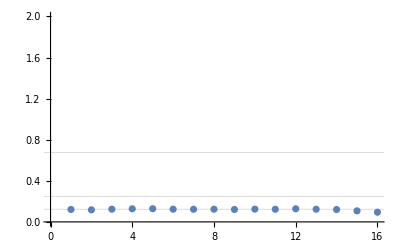

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum20free.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint=lisdt[[2;;21]];.10
p0=Abs[Table[ArcCosh[(twopoint[[i-1]]+twopoint[[i+1]])/(2*twopoint[[i]])],{i,2,17}]];
Mean[p0[[1;;14]]]
ListPlot[p0,GridLines->{{0,0,0},{0.249,.676, Mean[p0[[1;;14]]]}},PlotRange->{{0,2}}]
```

```mathematica
StandardDeviation[p0]/Sqrt[16]
```

0.00429194

0.95418

.10

0.174533

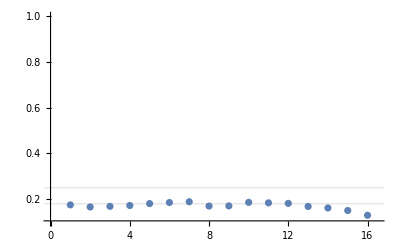

```mathematica
lisdt1=ReadList["~/GitHub/Lattice/zeromomentum201.txt",Number];
lisdt1[[1]]
Length[lisdt1];
twopoint1=lisdt1[[2;;21]];.10
p4=2*Abs[Table[ArcCosh[(twopoint1[[i-1]]+twopoint1[[i+1]])/(2*twopoint1[[i]])],{i,2,18}]];
Mean[p4[[1;;1]]]
ListPlot[p4,GridLines->{{0,0,0},{0.249, Mean[p4[[5;;13]]]}},PlotRange->{{0,16.5},{.1,1}}]
```

```mathematica
fits={{0.,2*0.12491876251115862},{0.3141592653589793,0.3353418862737486},{0.6283185307179586,0.6205436687803755},{0.9424777960769379,0.8871635352442027}};
```

```mathematica
r={{0,.2468},{Pi/10.,.706/2},{2*Pi/10.,1.23136/2},{3*Pi/10.,1.9113/2}};
```

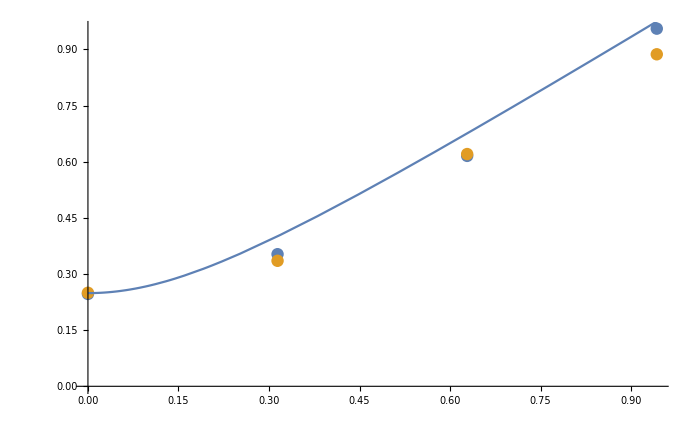

```mathematica
ListPlot[{r,fits},Epilog->{Plot[Sqrt[p^2+0.249^2],{p,0,10*Pi/10}][[1]]},PlotRange->All]
```

```mathematica
M[n_,m_]:=SparseArray[{Band[{1,n+1}]->(-1),Band[{n,1},{n*n,n*n},{n,n}]->(-1),{n,n+1}->(0),{n+1,n}->(0),Band[{n+1,n},{n*n-1,n*n},{n,n}]->(0),Band[{n,n+1},{n*n,n*n-1},{n,n}]->(0),Band[{1,1}]->(4+m^2),Band[{2,1}]->(-1.),Band[{1,2}]->(-1),Band[{n+1,1}]->(-1),Band[{n*n-n+1,1}]->(-1),Band[{1,n*n-n+1}]->(-1),Band[{1,n},{n*n,n*n},{n,n}]->(-1)},{n*n,n*n}]
IntM[n_,m_]:=Inverse[M[n,m]]
tay=IntM[20,.125];
```

0.962372

.10

0.165184

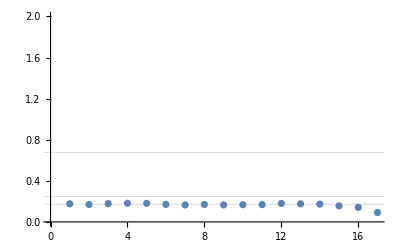

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum20001.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint001=lisdt[[2;;21]];.10
p3=Abs[Table[ArcCosh[(twopoint001[[i-1]]+twopoint001[[i+1]])/(2*twopoint001[[i]])],{i,2,18}]];
Mean[p3[[1;;17]]]
ListPlot[p3,GridLines->{{0,0,0},{0.249,.676, Mean[p3[[1;;14]]]}},PlotRange->{{0,2}}]
```

```mathematica
StandardDeviation[twopoint001]/Sqrt[16]
```

0.00896713

0.963244

.10

0.21108

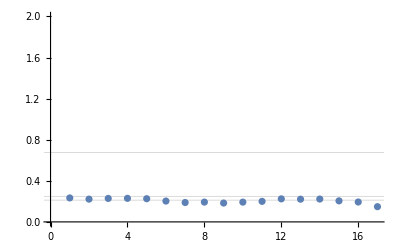

0.00658554

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum20003.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint003=lisdt[[2;;21]];.10
p4=Abs[Table[ArcCosh[(twopoint003[[i-1]]+twopoint003[[i+1]])/(2*twopoint003[[i]])],{i,2,18}]];
Mean[p4[[1;;13]]]
ListPlot[p4,GridLines->{{0,0,0},{0.249,.676, Mean[p4[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint003]/Sqrt[16]
```

0.964011

.10

0.263937

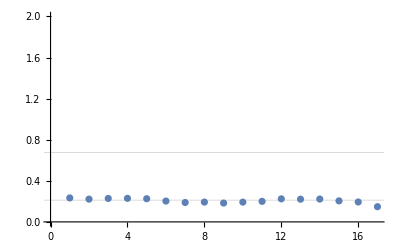

0.00467486

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum20005.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint007=lisdt[[2;;21]];.10
p5=Abs[Table[ArcCosh[(twopoint007[[i-1]]+twopoint007[[i+1]])/(2*twopoint007[[i]])],{i,2,17}]];
Mean[p5[[1;;14]]]
ListPlot[p4,GridLines->{{0,0,0},{.676, Mean[p4[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint007]/Sqrt[16]
```

0.964317

.10

0.292769

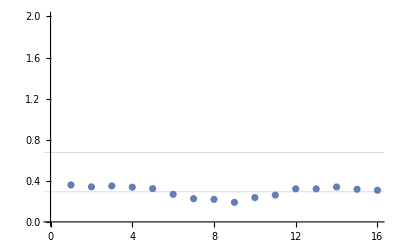

0.00395736

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum2001.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint01=lisdt[[2;;21]];.10
p1=Abs[Table[ArcCosh[(twopoint01[[i-1]]+twopoint01[[i+1]])/(2*twopoint01[[i]])],{i,2,17}]];
Mean[p1[[1;;14]]]
ListPlot[p1,GridLines->{{0,0,0},{.676, Mean[p1[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint01]/Sqrt[16]
```

0.964851

.10

0.335734

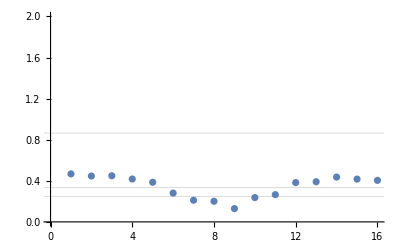

0.0266966

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum2002.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint02=lisdt[[2;;21]];.10
p02=Abs[Table[ArcCosh[(twopoint02[[i-1]]+twopoint02[[i+1]])/(2*twopoint02[[i]])],{i,2,17}]];
Mean[p02[[1;;14]]]
ListPlot[p02,GridLines->{{0,0,0},{0.249,.865, Mean[p02[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[p02]/Sqrt[16]
```

0.965108

.10

0.367935

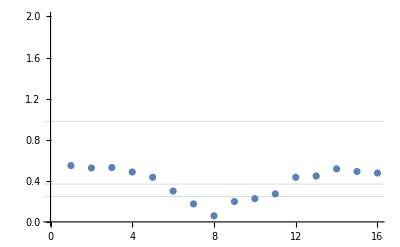

0.0383064

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum2003.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint03=lisdt[[2;;21]];.10
p03=Abs[Table[ArcCosh[(twopoint03[[i-1]]+twopoint03[[i+1]])/(2*twopoint03[[i]])],{i,2,17}]];
Mean[p03[[1;;14]]]
ListPlot[p03,GridLines->{{0,0,0},{0.249,.98, Mean[p03[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[p03]/Sqrt[16]
```

0.961567

.10

0.137631

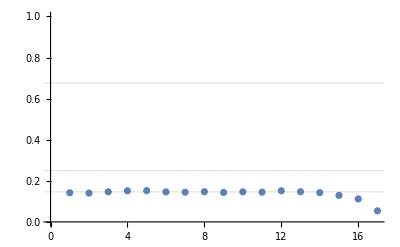

0.00589783

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum200002.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint0002=lisdt[[2;;21]];.10
p002=Abs[Table[ArcCosh[(twopoint0002[[i-1]]+twopoint0002[[i+1]])/(2*twopoint0002[[i]])],{i,2,18}]];
Mean[p002[[1;;17]]]
ListPlot[p002,GridLines->{{0,0,0},{0.249,.676, Mean[p002[[1;;14]]]}},PlotRange->{{0,1}}]
StandardDeviation[p002[[1;;17]]]/Sqrt[16]
```

0.961985

.10

0.150895

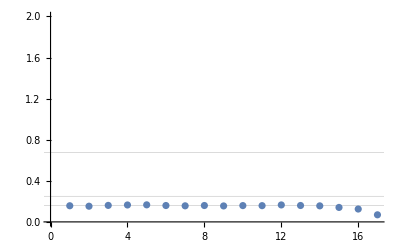

0.0101554

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum200006.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint0006=lisdt[[2;;21]];.10
p006=Abs[Table[ArcCosh[(twopoint0006[[i-1]]+twopoint0006[[i+1]])/(2*twopoint0006[[i]])],{i,2,18}]];
Mean[p006[[1;;17]]]
ListPlot[p006,GridLines->{{0,0,0},{0.249,.676, Mean[p006[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint0006]/Sqrt[16]
```

0.962179

.10

0.165371

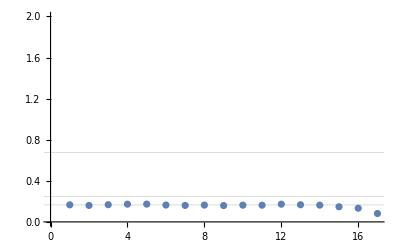

0.00953128

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum200008.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint0008=lisdt[[2;;21]];.10
p008=Abs[Table[ArcCosh[(twopoint0008[[i-1]]+twopoint0008[[i+1]])/(2*twopoint0008[[i]])],{i,2,18}]];
Mean[p008[[1;;14]]]
ListPlot[p008,GridLines->{{0,0,0},{0.249,.676, Mean[p008[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint0008]/Sqrt[16]
```

0.960859

.10

0.124472

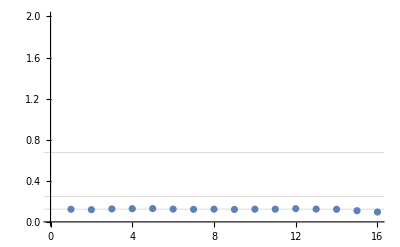

0.0135654

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum200001.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint0001=lisdt[[2;;21]];.10
p001=Abs[Table[ArcCosh[(twopoint0001[[i-1]]+twopoint0001[[i+1]])/(2*twopoint0001[[i]])],{i,2,17}]];
Mean[p001[[1;;14]]]
ListPlot[p001,GridLines->{{0,0,0},{0.249,.676, Mean[p001[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint0001]/Sqrt[16]
```

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum2000005.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint00005=lisdt[[2;;21]];.10
p0005=Abs[Table[ArcCosh[(twopoint00005[[i-1]]+twopoint00005[[i+1]])/(2*twopoint00005[[i]])],{i,2,17}]];
Mean[p0005[[1;;14]]]
ListPlot[p0005,GridLines->{{0,0,0},{0.249,.676, Mean[p0005[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint00005]/Sqrt[16]
```

0.960859

.10

0.124472

-Graphics-

0.0135654

0.961314

.10

0.136154

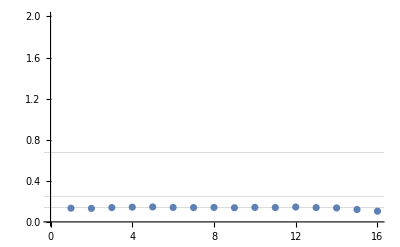

0.0121292

```mathematica
lisdt=ReadList["~/GitHub/Lattice/zeromomentum2000007.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint00007=lisdt[[2;;21]];.10
p0007=Abs[Table[ArcCosh[(twopoint00007[[i-1]]+twopoint00007[[i+1]])/(2*twopoint00007[[i]])],{i,2,17}]];
Mean[p0007[[1;;16]]]
ListPlot[p0007,GridLines->{{0,0,0},{0.249,.676, Mean[p0007[[1;;14]]]}},PlotRange->{{0,2}}]
StandardDeviation[twopoint00007]/Sqrt[16]
```

```mathematica
Vals={{0,Mean[p0[[1;;14]]]},{0.002,Mean[p002[[1;;17]]]},{0.006,Mean[p006[[1;;16]]]},{0.008,Mean[p008[[1;;14]]]},{0.01,Mean[p3[[1;;14]]]},{0.03,Mean[p4[[1;;14]]]},{0.07,Mean[p5[[1;;16]]]},{0.1,Mean[p1[[1;;16]]]},{0.2,Mean[p02[[1;;16]]]},{0.3,Mean[p03[[1;;16]]]}};
```

```mathematica
err={StandardDeviation[p0]/Sqrt[16],StandardDeviation[p002]/Sqrt[16],StandardDeviation[p006]/Sqrt[16],StandardDeviation[p008]/Sqrt[16],StandardDeviation[p3]/Sqrt[16],StandardDeviation[p4]/Sqrt[16],StandardDeviation[p5]/Sqrt[16],StandardDeviation[p1]/Sqrt[16],StandardDeviation[p02]/Sqrt[16],StandardDeviation[p03]/Sqrt[16]};
```

```mathematica
Mlambda=Table[{Vals[[i]],ErrorBar[err[[i]]]},{i,1,Length[Vals]}];
```

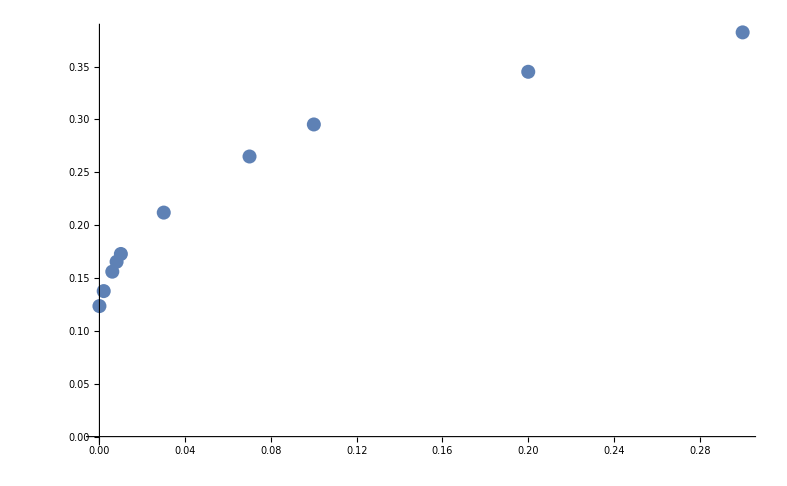

```mathematica
ListPlot[Vals,PlotRange->All]
```

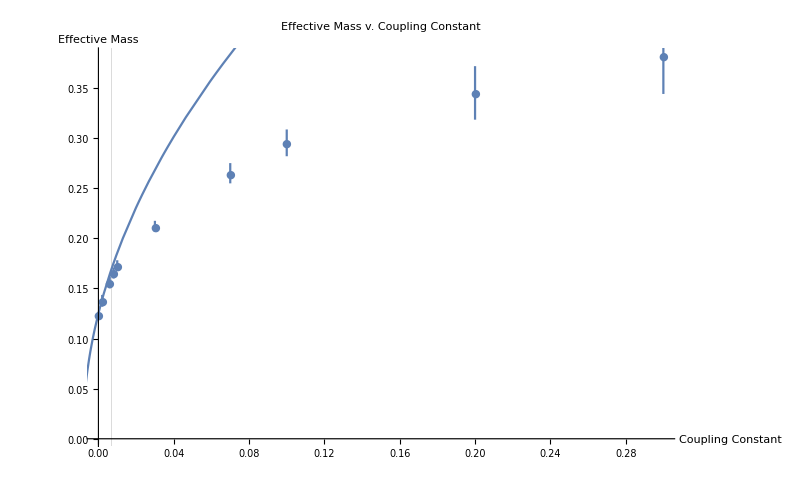

```mathematica
g=ErrorListPlot[Mlambda,PlotLabel->"Effective Mass v. Coupling Constant",AxesLabel->{"Coupling Constant","Effective Mass"},PlotRange->Full,GridLines->{{0,0.007},{0,0}}, PlotMarkers->{Automatic,Small},Epilog->{Plot[{Sqrt[0.125^2+1.88*x]},{x,-1,0.3}][[1]]}]
```

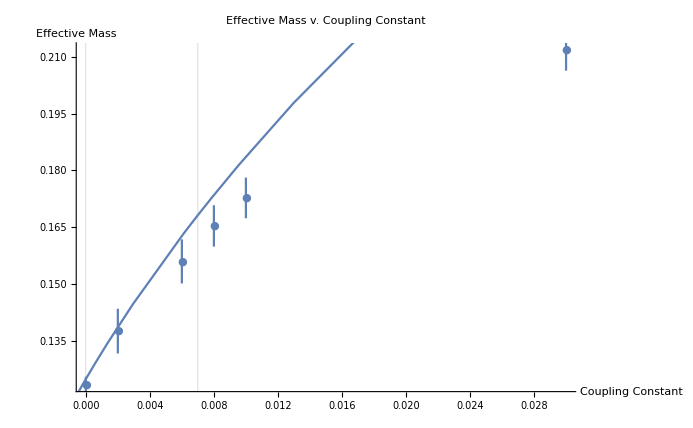

```mathematica
h=ErrorListPlot[Mlambda[[1;;6]],PlotLabel->"Effective Mass v. Coupling Constant",AxesLabel->{"Coupling Constant","Effective Mass"},PlotRange->Full,GridLines->{{0,0.007},{0,0}}, PlotMarkers->{Automatic,Small},Epilog->{Plot[{Sqrt[0.125^2+1.81*x]},{x,-1,0.3}][[1]]}]
```

```mathematica
Export["~/GitHub/Lattice/MvLplusfitzoom.pdf",h]
```

~/GitHub/Lattice/MvLplusfitzoom.pdf

0.960714

.10

0.121649

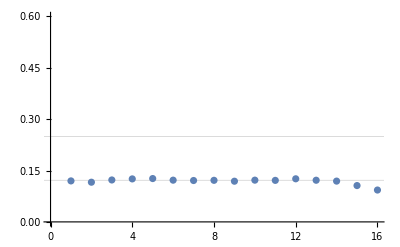

0.00215718

/Users/Taylor

```mathematica
lisdt=ReadList["~/GitHub/Lattice/test.txt",Number];
lisdt[[1]]
Length[lisdt];
twopoint00007=lisdt[[2;;20]];.10
p0007=Abs[Table[ArcCosh[(twopoint00007[[i-1]]+twopoint00007[[i+1]])/(2*twopoint00007[[i]])],{i,2,17}]];
Mean[p0007[[1;;14]]]
ListPlot[p0007,GridLines->{{0,0,0},{0.249,Mean[p0007[[1;;14]]]}},PlotRange->{{0,0.6}}]
StandardDeviation[p0007/Sqrt[15]]
"/Users/Taylor"
```

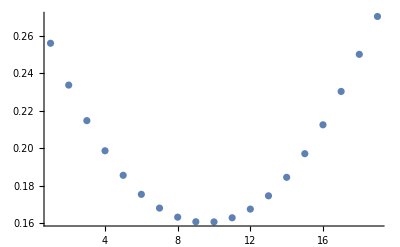

```mathematica
ListPlot[twopoint00007,PlotRange->All]
```

```mathematica
w=FindFit[Vals,A*Sqrt[x]+b,{A,b},x];
```

```mathematica
.006/.137
```

0.0437956

## Hopefully, When I was Less Stupid

### Autocorrelation

```mathematica
cor11=Table[momcor[[i]][[1]],{i,1,Length[momcor]}];
```

```mathematica
m=Mean[cor11];
v=Variance[cor11];
```

```mathematica
Length[cor11]
```

```mathematica
auto=Table[(Mean[cor11[[i;;]]cor11[[;;-i]]]-m^2)/v,{i,0,500}];
```

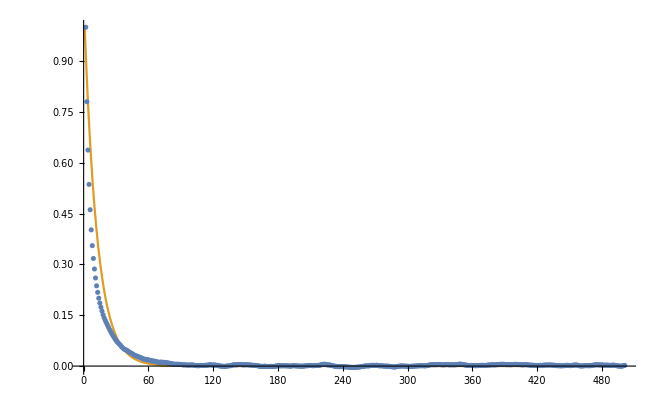

```mathematica
ListPlot[{auto,fit},PlotRange->Full,Joined->{False,True}]
```

```mathematica
fit=Table[Exp[-t/12],{t,0,500}];
```

### λ = 0

```mathematica
JackknifeBin[transcor[1],Mean,600]
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
compcorr=Table[JackknifeBin[transcor[[i]],Mean,1000],{i,1,Length[transcor]}];
```

```mathematica
compcorr;
```

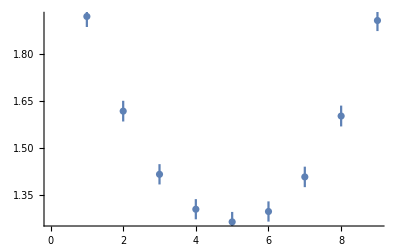

```mathematica
ErrorListPlot[compcorr]
```

```mathematica
JackknifeBinCov[transcor,Mean,1]
```

```mathematica
steve=FindFit[Transpose[{Range[Length[Transpose[compcorr][[1]]]]-Length[Transpose[compcorr][[1]]]/2-1/2,Transpose[compcorr][[1]]}],A*Cosh[m t],{A,m},t]
```

{A→1.26102,m→0.243924}

```mathematica
joe=Transpose[Join[{Range[Length[Transpose[compcorr][[1]]]]-Length[Transpose[compcorr][[1]]]/2-1/2,Transpose[compcorr][[1]]},{Transpose[compcorr][[2]]}]];
```

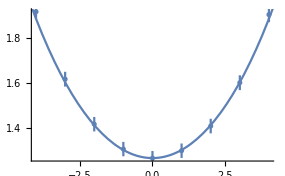

```mathematica
ErrorListPlot[joe,Epilog->{Plot[(BestFitFunction/.lou)@t,{t,-5,5}][[1]]}]
```

```mathematica
{vals,cov}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou=FitModel[Transpose[{Range[Length[vals]]-(Length[vals]+1)/2,vals}],cov,(A*Cosh[q*#])&,{{A,1},{q,1}},3,7];
```

```mathematica
PrintFitReport[lou]
```

Hessian=(6554.78 | 49079.7
49079.7 | 534014.)	Δ=(0.000982625 | -0.0000904832
-0.0000904832 | 0.0000120844)	CovMat=(1. | -0.830352
 | 1.)

χ^2=4.7524   χ^2/dof=0.678914

Confidence level=0.69015

Final Results
 | Best fit | Error
A | 1.25626 | 0.0313469
m | 0.246394 | 0.00347626

### λ = 0.005

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda0005.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.62862

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals0005,cov0005}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou0005=FitModel[Transpose[{Range[Length[vals0005]]-(Length[vals0005]+1)/2,vals0005}],cov0005,(A*Cosh[q*#])&,{{A,1},{q,1}},1,9];
```

```mathematica
PrintFitReport[lou0005]
```

Hessian=(9234.42 | 56711.7
56711.7 | 503526.)	Δ=(0.000704172 | -0.000079395
-0.000079395 | 0.000012928)	CovMat=(1. | -0.832125
 | 1.)

χ^2=2.21184   χ^2/dof=0.315977

Confidence level=0.947191

Final Results
 | Best fit | Error
A | 1.07407 | 0.0265362
q | 0.262209 | 0.00359555

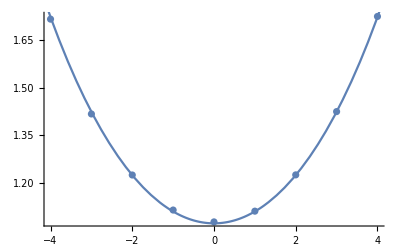

```mathematica
ListPlot[Transpose[{Range[Length[vals0005]]-(Length[vals0005]+1)/2,vals0005}],Epilog->{Plot[(BestFitFunction/.lou0005)@t,{t,-5,5}][[1]]}]
```

### λ = 0.01

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda001.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.628369

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals001,cov001}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou001=FitModel[Transpose[{Range[Length[vals001]]-(Length[vals001]+1)/2,vals001}],cov001,(A*Cosh[q*#])&,{{A,1},{q,1}},1,9];
```

```mathematica
PrintFitReport[lou001]
```

Hessian=(13130.9 | 69169.6
69169.6 | 517991.)	Δ=(0.000516825 | -0.0000691974
-0.0000691974 | 0.0000131361)	CovMat=(1. | -0.839816
 | 1.)

χ^2=6.27828   χ^2/dof=0.896897

Confidence level=0.507658

Final Results
 | Best fit | Error
A | 0.975318 | 0.0227338
q | 0.273166 | 0.00362438

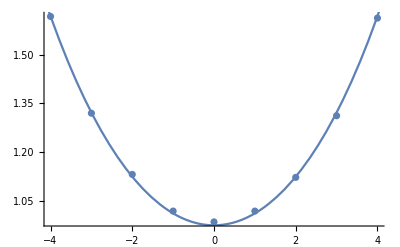

```mathematica
ListPlot[Transpose[{Range[Length[vals001]]-(Length[vals001]+1)/2,vals001}],Epilog->{Plot[(BestFitFunction/.lou001)@t,{t,-5,5}][[1]]}]
```

### λ = 0.02

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda002.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.62799

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals002,cov002}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou002=FitModel[Transpose[{Range[Length[vals002]]-(Length[vals002]+1)/2,vals002}],cov002,(A*Cosh[q*#])&,{{A,1},{q,1}},1,9];
```

```mathematica
PrintFitReport[lou002]
```

Hessian=(20184.9 | 81926.
81926. | 481359.)	Δ=(0.000321227 | -0.0000547316
-0.0000547316 | 0.0000134847)	CovMat=(1. | -0.831592
 | 1.)

χ^2=2.97292   χ^2/dof=0.424703

Confidence level=0.887496

Final Results
 | Best fit | Error
A | 0.775228 | 0.0179228
q | 0.299266 | 0.00367216

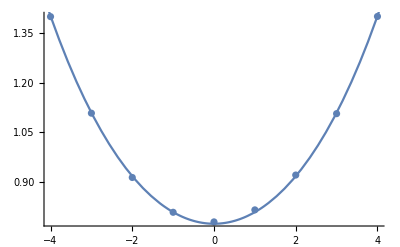

```mathematica
ListPlot[Transpose[{Range[Length[vals002]]-(Length[vals002]+1)/2,vals002}],Epilog->{Plot[(BestFitFunction/.lou002)@t,{t,-5,5}][[1]]}]
```

### λ = 0.03

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda003.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.627548

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals003,cov003}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou003=FitModel[Transpose[{Range[Length[vals003]]-(Length[vals003]+1)/2,vals003}],cov003,(A*Cosh[q*#])&,{{A,1},{q,1}},1,9];
```

```mathematica
PrintFitReport[lou003]
```

Hessian=(34385.4 | 112850.
112850. | 490973.)	Δ=(0.000238105 | -0.0000548279
-0.0000548279 | 0.000016706)	CovMat=(1. | -0.869322
 | 1.)

χ^2=2.20489   χ^2/dof=0.314984

Confidence level=0.947635

Final Results
 | Best fit | Error
A | 0.638033 | 0.0154307
q | 0.321709 | 0.0040873

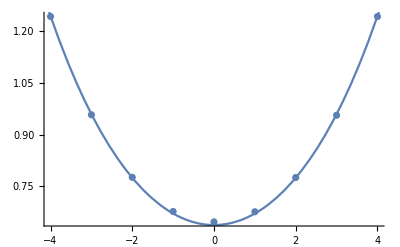

```mathematica
ListPlot[Transpose[{Range[Length[vals003]]-(Length[vals003]+1)/2,vals003}],Epilog->{Plot[(BestFitFunction/.lou003)@t,{t,-5,5}][[1]]}]
```

### λ = 0.04

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda004.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

-4.09716

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals004,cov004}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou004=FitModel[Transpose[{Range[Length[vals004]]-(Length[vals004]+1)/2,vals004}],cov004,(A*Cosh[q*#])&,{{A,1},{q,1}},2,8];
```

```mathematica
PrintFitReport[lou004]
```

Hessian=(26240.6 | 49950.3
49950.3 | 151537.)	Δ=(0.000205028 | -0.0000676683
-0.0000676683 | 0.0000355485)	CovMat=(1. | -0.792626
 | 1.)

χ^2=1.72613   χ^2/dof=0.345226

Confidence level=0.885591

Final Results
 | Best fit | Error
A | 0.560188 | 0.0143188
q | 0.331643 | 0.00596225

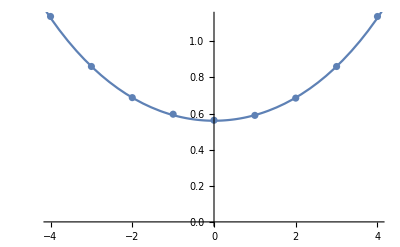

```mathematica
ListPlot[Transpose[{Range[Length[vals004]]-(Length[vals004]+1)/2,vals004}],Epilog->{Plot[(BestFitFunction/.lou004)@t,{t,-5,5}][[1]]}]
```

### λ = 0.05

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda005.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.626872

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals005,cov005}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou005=FitModel[Transpose[{Range[Length[vals005]]-(Length[vals005]+1)/2,vals005}],cov005,(A*Cosh[q*#])&,{{A,1},{q,1}},3,7];
```

```mathematica
PrintFitReport[lou005]
```

Hessian=(26015.4 | 24964.5
24964.5 | 45839.4)	Δ=(0.000161033 | -0.0000876982
-0.0000876982 | 0.0000913899)	CovMat=(1. | -0.722909
 | 1.)

χ^2=0.855157   χ^2/dof=0.285052

Confidence level=0.836234

Final Results
 | Best fit | Error
A | 0.479095 | 0.0126899
q | 0.353844 | 0.00955981

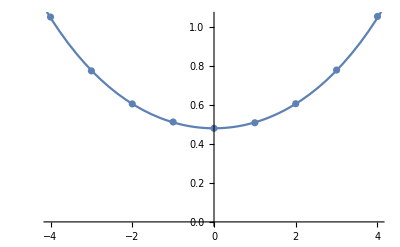

```mathematica
ListPlot[Transpose[{Range[Length[vals005]]-(Length[vals005]+1)/2,vals005}],Epilog->{Plot[(BestFitFunction/.lou005)@t,{t,-5,5}][[1]]}]
```

### λ = 0.1

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda01.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

-3.89584

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals01,cov01}=JackknifeBinCov[momcor,Mean,500];
```

```mathematica
lou01=FitModel[Transpose[{Range[Length[vals01]]-(Length[vals01]+1)/2,vals01}],cov01,(A*Cosh[q*#])&,{{A,1},{q,1}},1,9];
```

```mathematica
PrintFitReport[lou01]
```

Hessian=(231935. | 287671.
287671. | 425407.)	Δ=(0.0000537266 | -0.0000363648
-0.0000363648 | 0.0000293192)	CovMat=(1. | -0.916242
 | 1.)

χ^2=2.70759   χ^2/dof=0.386799

Confidence level=0.910672

Final Results
 | Best fit | Error
A | 0.274264 | 0.00732984
q | 0.429403 | 0.00541472

```mathematica
cov01[[2]][[2]]
```

0.0000845912

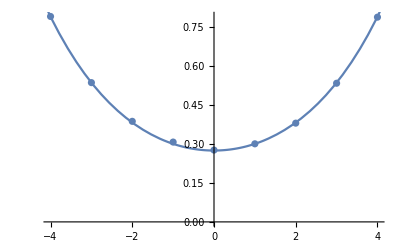

```mathematica
ErrorListPlot[Transpose[{Range[Length[vals01]]-(Length[vals01]+1)/2,vals01,Table[cov01[[i]][[i]],{i,1,Length[vals01]}]}],Epilog->{Plot[(BestFitFunction/.lou01)@t,{t,-5,5}][[1]]}]
```

### λ = 1

```mathematica
momcor=ReadList["~/GitHub/Lattice/lambda1.txt", Number];
```

```mathematica
momcor[[-1]]
momcor=Drop[momcor,-1];
```

0.608308

```mathematica
momcor=Partition[momcor,9];
```

```mathematica
transcor=Transpose[momcor];
```

```mathematica
{vals2,cov2}=JackknifeBinCov[momcor,Mean,1000];
```

```mathematica
lou2=FitModel[Transpose[{Range[Length[vals2]]-(Length[vals2]+1)/2,vals2}],cov2,(A*Cosh[q*#])&,{{A,1},{q,2}},1,9];
```

Hessian=(9.82987×10^7 | 5.23586×10^6
5.23586×10^6 | 285573.)	Δ=(8.66488×10^-7 | -0.0000158856
-0.0000158856 | 0.000298238)	CovMat=(1. | -0.98819
 | 1.)

χ^2=6.77054   χ^2/dof=0.96722

Confidence level=0.453156

Final Results
 | Best fit | Error
A | 0.0129335 | 0.000930853
q | 0.874764 | 0.0172696

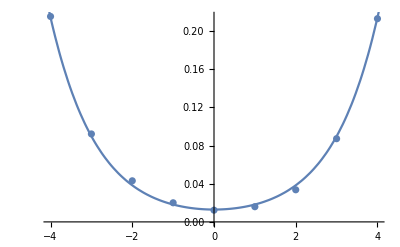

```mathematica
PrintFitReport[lou2]
ListPlot[Transpose[{Range[Length[vals2]]-(Length[vals2]+1)/2,vals2}],Epilog->{Plot[(BestFitFunction/.lou2)@t,{t,-5,5}][[1]]},PlotRange->All]
```

### Plotting and Perturbative Approximations

```mathematica
interactingmass={{0,0.246,0.004},{0.005,0.2622,0.004},{0.01,0.274,0.004},{0.02,0.299,0.004},{0.03,0.321,0.004},{0.04,0.331,0.006},{0.05,0.353,0.009}(*,{1,0.87,0.01}*)};
```

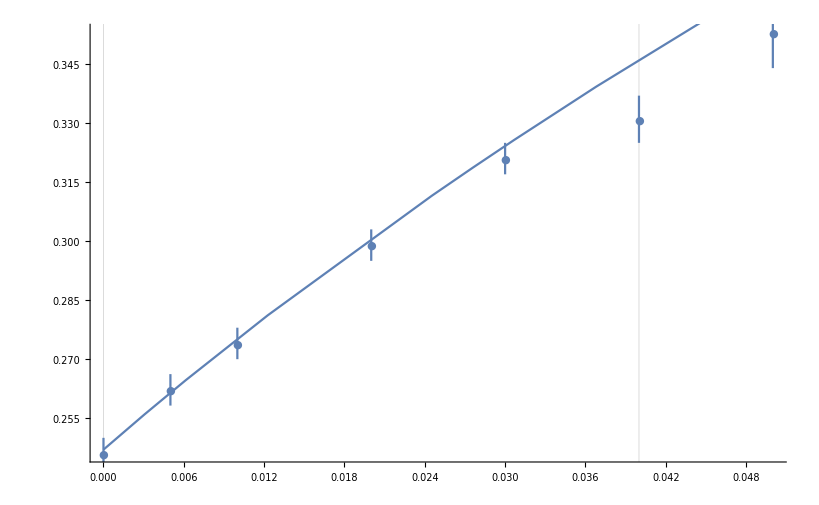

```mathematica
ErrorListPlot[interactingmass,Epilog->{Plot[f[x],{x,0,10}][[1]]},PlotMarkers->{Automatic,Small},GridLines->{{0.04,0},{0,0}},PlotRange->All]
```

```mathematica
f[x_]:=Sqrt[0.247^2+1.47*x];
```

## Symmetry Breaking

## L = 10

### Discrete Symmetry Breaking in 1+1

#### Plot of Positive Mass

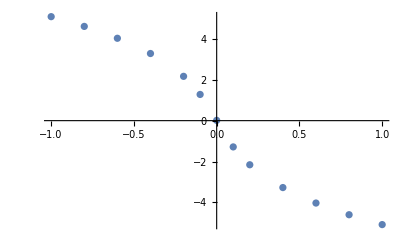

```mathematica
ErrorListPlot[{{1,val1,err1},{0.8,val8,err8},{0.6,val6,err6},{0.4,val4,err4},{0.2,val2,err2},{0.1,val01,err01},{0,val0,err0},{-0.1,valn1,errn1},{-0.2,valn2,errn2},{-0.4,valn4,errn4},{-0.6,valn6,errn6},{-1,valn10,errn10},{-0.8,valn8,errn8}}]
```

```mathematica
joe={{1,val1,err1},{0.8,val8,err8},{0.6,val6,err6},{0.4,val4,err4},{0.2,val2,err2},{0.1,val01,err01},{0,val0,err0},{-0.1,valn1,errn1},{-0.2,valn2,errn2},{-0.4,valn4,errn4},{-0.6,valn6,errn6},{-1,valn10,errn10},{-0.8,valn8,errn8}};
```

#### Plot of Negtive Mass

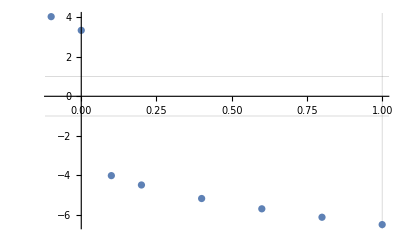

```mathematica
ErrorListPlot[{{1,nval1,nerr1},{0.8,nval8,nerr8},{0.6,nval6,nerr6},{0.4,nval4,nerr4},{0.2,nval2,nerr2},{0.1,nval01,nerr01},{0,nval0,nerr0},{-0.1,nvaln1,nerrn1}(*,{-0.2,valn2,errn2},{-0.4,valn4,errn4},{-0.6,valn6,errn6},{-1,valn10,errn10},{-0.8,valn8,errn8}*)},GridLines->{{-1,0,1}, {-1,0,1}}]
```

### Evaluation of vevs for positive m

#### h = 1; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2x^2+λ/4x^4;
```

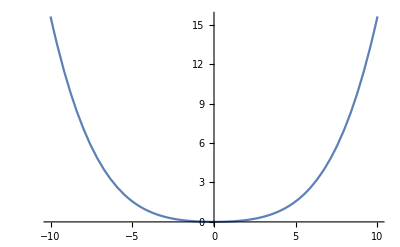

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

```mathematica
avg=ReadList["~/GitHub/Lattice/testh.txt",Number];
```

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-5.08479

```mathematica
Variance[avg]
```

0.0222934

```mathematica
{val1,err1}=JackknifeBin[avg,Mean,200]
```

{-5.0848,0.0010325}

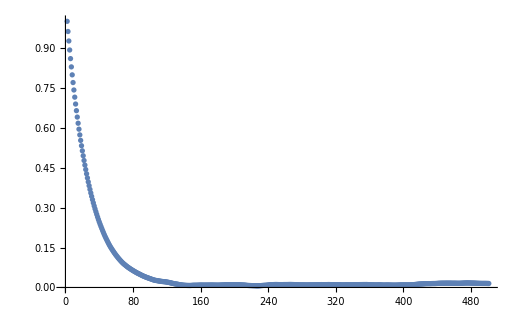

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

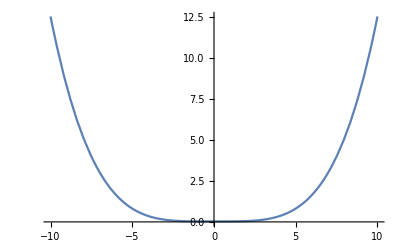

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

```mathematica
avg=ReadList["~/GitHub/Lattice/h8.txt",Number];
```

```mathematica
avg[[-1]]
```

0.616764

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-4.60233

```mathematica
Variance[avg]
```

0.0253324

```mathematica
{val8,err8}=JackknifeBin[avg,Mean,200]
```

{-4.60222,0.0036697}

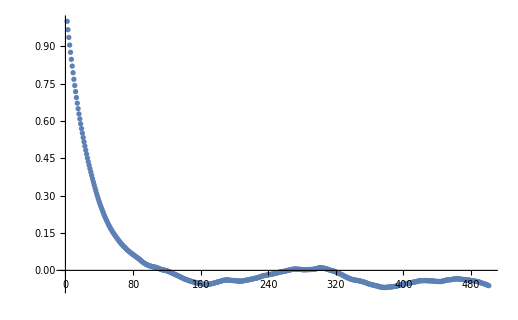

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h6.txt",Number];
```

```mathematica
avg[[-1]]
```

0.619349

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-4.03067

```mathematica
Variance[avg]
```

0.0315575

```mathematica
{val6,err6}=JackknifeBin[avg,Mean,200]
```

{-4.03073,0.00452424}

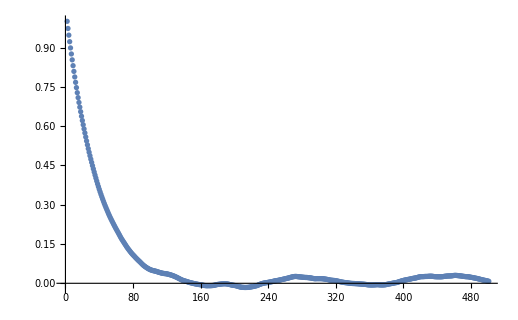

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h4.txt",Number];
```

```mathematica
avg[[-1]]
```

0.622371

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-3.27326

```mathematica
Variance[avg]
```

0.0436973

```mathematica
{val4,err4}=JackknifeBin[avg,Mean,200]
```

{-3.27316,0.00578514}

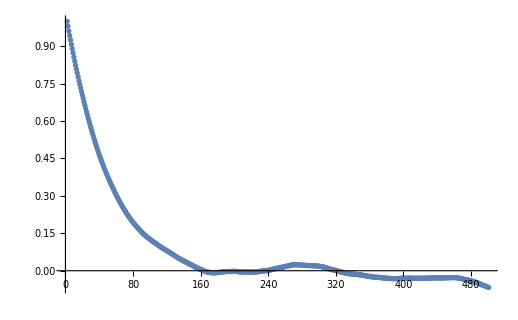

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.625959

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-2.15832

```mathematica
Variance[avg]
```

0.0740779

```mathematica
{val2,err2}=JackknifeBin[avg,Mean,400]
```

{-2.15818,0.00998807}

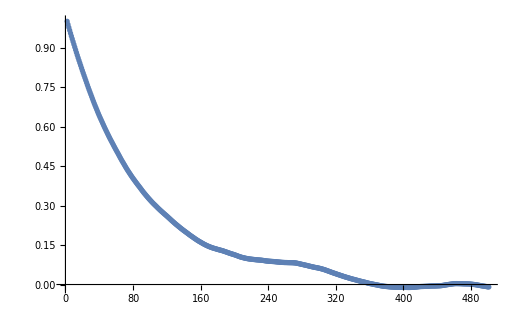

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h1.txt",Number];
```

```mathematica
avg[[-1]]
```

0.627672

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-1.28555

```mathematica
Variance[avg]
```

0.103366

```mathematica
{val01,err01}=JackknifeBin[avg,Mean,500]
```

{-1.28507,0.0143186}

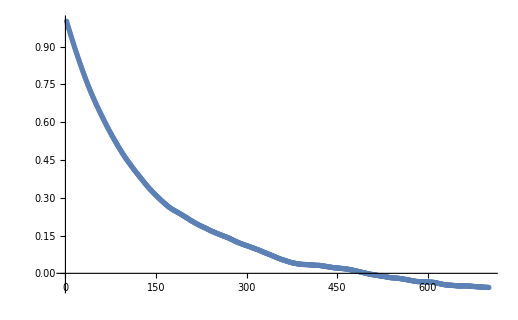

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h0.txt",Number];
```

```mathematica
avg[[-1]]
```

0.628423

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

0.013543

```mathematica
Variance[avg]
```

0.132756

```mathematica
{val0,err0}=JackknifeBin[avg,Mean,700]
```

{0.0140712,0.0184073}

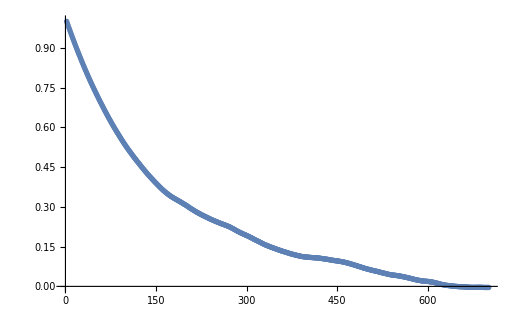

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn1.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.62765

1.281

0.100041

```mathematica
{valn1,errn1}=JackknifeBin[avg,Mean,500]
```

{1.28133,0.0139128}

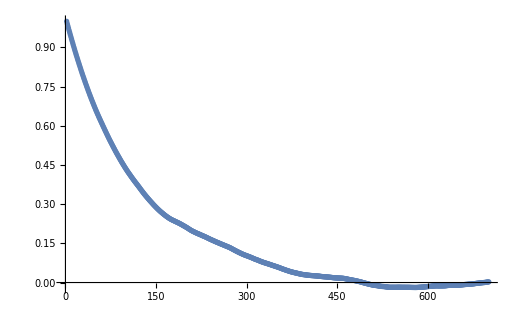

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.626038

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

2.16738

```mathematica
Variance[avg]
```

0.0687108

```mathematica
{valn2,errn2}=JackknifeBin[avg,Mean,400]
```

{2.16758,0.00919878}

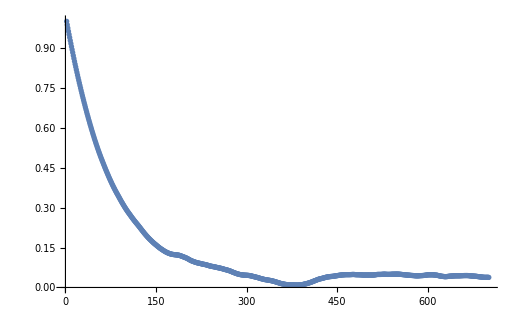

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.622497

3.28394

0.043094

```mathematica
{valn4,errn4}=JackknifeBin[avg,Mean,300]
```

{3.28409,0.00585149}

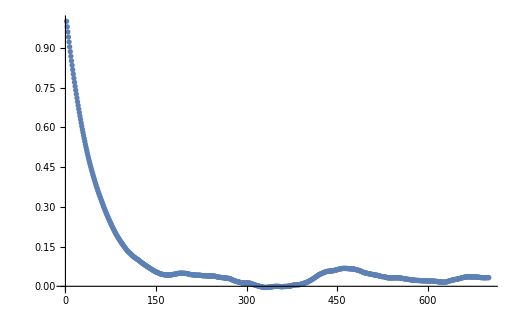

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.619431

4.02978

0.0319982

```mathematica
{valn6,errn6}=JackknifeBin[avg,Mean,300]
```

{4.0299,0.00452078}

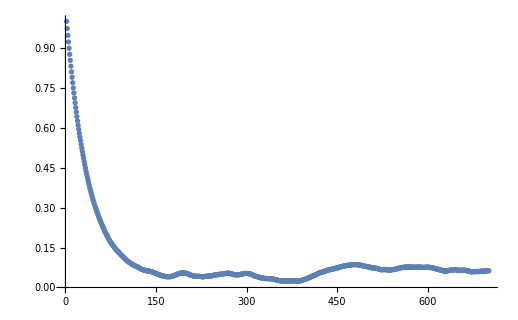

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61664

4.61015

0.0251912

```mathematica
{valn8,errn8}=JackknifeBin[avg,Mean,300]
```

{4.61014,0.00355442}

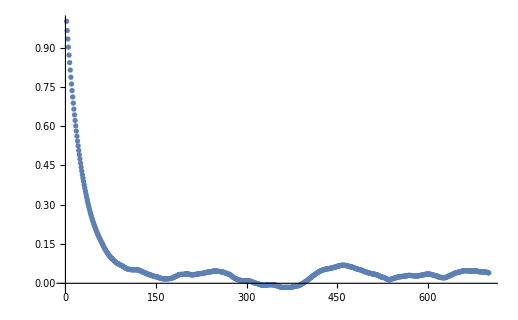

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 1.0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn10.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61413

5.08695

0.0218206

```mathematica
{valn10,errn10}=JackknifeBin[avg,Mean,300]
```

{5.08707,0.00304846}

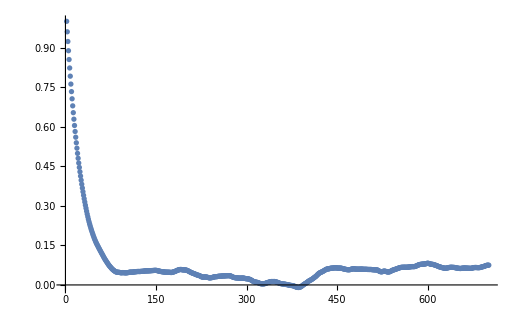

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

### Evaluation of vevs for negative m

#### h = 1; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2* x^2+λ/4x^4;
```

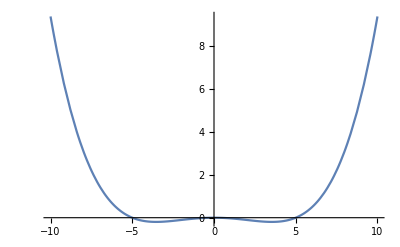

```mathematica
Plot[V1[.25,0.005,x],{x,-10,10}]
```

```mathematica
avg=ReadList["~/GitHub/Lattice/nh1.txt",Number];
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

-6.50557

0.0173243

```mathematica
{nval1,nerr1}=JackknifeBin[avg,Mean,100]
```

{-6.50549,0.00236353}

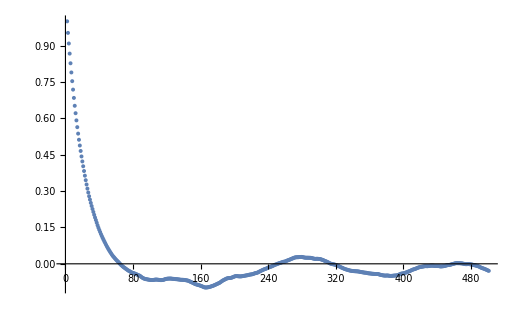

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2*x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.612387

-6.13275

0.0195687

```mathematica
{nval8,nerr8}=JackknifeBin[avg,Mean,200]
```

{-6.1327,0.00286134}

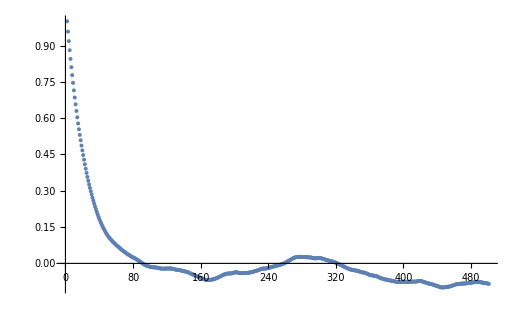

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.615109

-5.70569

0.0228621

```mathematica
{nval6,nerr6}=JackknifeBin[avg,Mean,200]
```

{-5.70564,0.00342108}

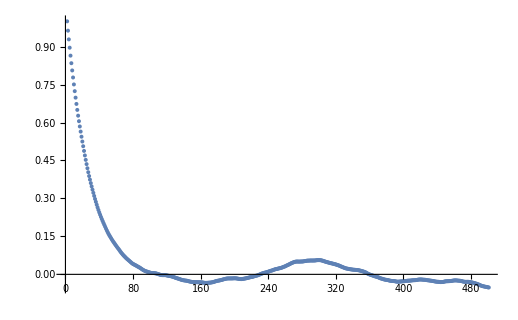

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.618205

-5.18364

0.0290582

```mathematica
{nval4,nerr4}=JackknifeBin[avg,Mean,200]
```

{-5.18357,0.00417071}

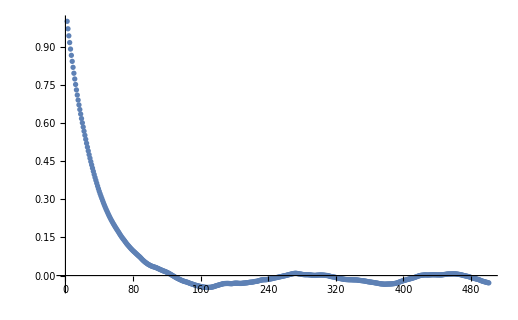

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh2.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.621779

-4.49729

0.0405251

```mathematica
{nval2,nerr2}=JackknifeBin[avg,Mean,300]
```

{-4.49723,0.00569407}

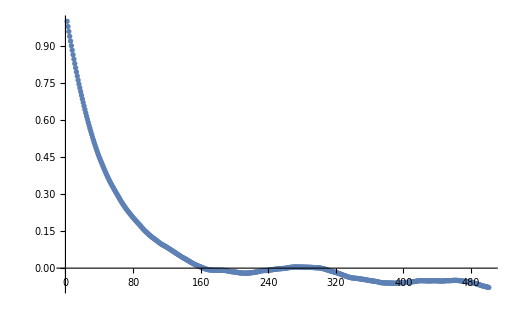

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh1.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.624201

-4.02343

0.0520455

```mathematica
{nval01,nerr01}=JackknifeBin[avg,Mean,500]
```

{-4.023,0.00772795}

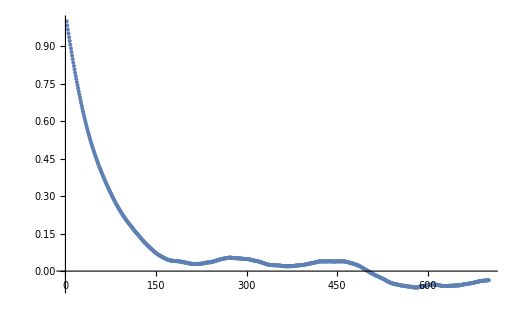

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh0.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.627035

3.34311

0.0898327

```mathematica
{nval0,nerr0}=JackknifeBin[avg,Mean,700]
```

{3.34354,0.0124417}

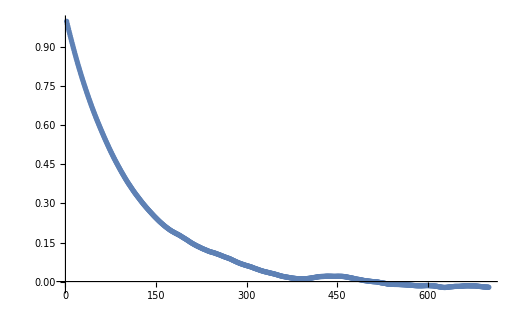

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh01.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.624051

4.03749

0.0530703

```mathematica
{nvaln1,nerrn1}=JackknifeBin[avg,Mean,300]
```

{4.03741,0.00704523}

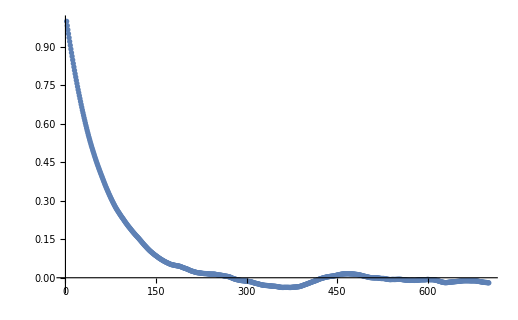

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = -0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.626038

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

2.16738

```mathematica
Variance[avg]
```

0.0687108

```mathematica
{valn2,errn2}=JackknifeBin[avg,Mean,400]
```

{2.16758,0.00919878}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.622497

3.28394

0.043094

```mathematica
{valn4,errn4}=JackknifeBin[avg,Mean,300]
```

{3.28409,0.00585149}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.619431

4.02978

0.0319982

```mathematica
{valn6,errn6}=JackknifeBin[avg,Mean,300]
```

{4.0299,0.00452078}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61664

4.61015

0.0251912

```mathematica
{valn8,errn8}=JackknifeBin[avg,Mean,300]
```

{4.61014,0.00355442}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 1.0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn10.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61413

5.08695

0.0218206

```mathematica
{valn10,errn10}=JackknifeBin[avg,Mean,300]
```

{5.08707,0.00304846}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

## L = 16

### Evaluation of vevs for positive m

#### h = 1; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/testh.txt",Number];
```

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-5.08479

```mathematica
Variance[avg]
```

0.0222934

```mathematica
{val1,err1}=JackknifeBin[avg,Mean,200]
```

{-5.0848,0.0010325}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h8.txt",Number];
```

```mathematica
avg[[-1]]
```

0.616764

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-4.60233

```mathematica
Variance[avg]
```

0.0253324

```mathematica
{val8,err8}=JackknifeBin[avg,Mean,200]
```

{-4.60222,0.0036697}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h6.txt",Number];
```

```mathematica
avg[[-1]]
```

0.619349

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-4.03067

```mathematica
Variance[avg]
```

0.0315575

```mathematica
{val6,err6}=JackknifeBin[avg,Mean,200]
```

{-4.03073,0.00452424}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h4.txt",Number];
```

```mathematica
avg[[-1]]
```

0.622371

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-3.27326

```mathematica
Variance[avg]
```

0.0436973

```mathematica
{val4,err4}=JackknifeBin[avg,Mean,200]
```

{-3.27316,0.00578514}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.625959

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-2.15832

```mathematica
Variance[avg]
```

0.0740779

```mathematica
{val2,err2}=JackknifeBin[avg,Mean,400]
```

{-2.15818,0.00998807}

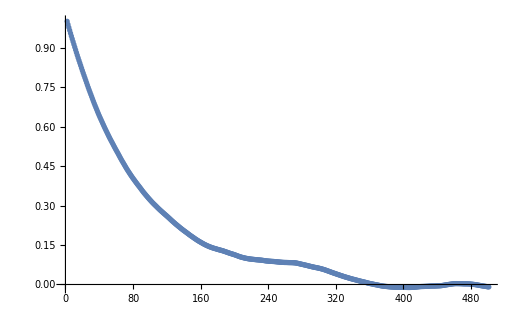

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

#### h = 0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h1.txt",Number];
```

```mathematica
avg[[-1]]
```

0.627672

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

-1.28555

```mathematica
Variance[avg]
```

0.103366

```mathematica
{val01,err01}=JackknifeBin[avg,Mean,500]
```

{-1.28507,0.0143186}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/h0.txt",Number];
```

```mathematica
avg[[-1]]
```

0.628423

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

0.013543

```mathematica
Variance[avg]
```

0.132756

```mathematica
{val0,err0}=JackknifeBin[avg,Mean,700]
```

{0.0140712,0.0184073}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn1.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.62765

1.281

0.100041

```mathematica
{valn1,errn1}=JackknifeBin[avg,Mean,500]
```

{1.28133,0.0139128}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.626038

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

2.16738

```mathematica
Variance[avg]
```

0.0687108

```mathematica
{valn2,errn2}=JackknifeBin[avg,Mean,400]
```

{2.16758,0.00919878}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.622497

3.28394

0.043094

```mathematica
{valn4,errn4}=JackknifeBin[avg,Mean,300]
```

{3.28409,0.00585149}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.619431

4.02978

0.0319982

```mathematica
{valn6,errn6}=JackknifeBin[avg,Mean,300]
```

{4.0299,0.00452078}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61664

4.61015

0.0251912

```mathematica
{valn8,errn8}=JackknifeBin[avg,Mean,300]
```

{4.61014,0.00355442}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 1.0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn10.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61413

5.08695

0.0218206

```mathematica
{valn10,errn10}=JackknifeBin[avg,Mean,300]
```

{5.08707,0.00304846}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

### Evaluation of vevs for negative m

#### h = 1; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2* x^2+λ/4x^4;
```

```mathematica
Plot[V1[.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh1.txt",Number];
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

-6.50557

0.0173243

```mathematica
{nval1,nerr1}=JackknifeBin[avg,Mean,100]
```

{-6.50549,0.00236353}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2*x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.612387

-6.13275

0.0195687

```mathematica
{nval8,nerr8}=JackknifeBin[avg,Mean,200]
```

{-6.1327,0.00286134}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.615109

-5.70569

0.0228621

```mathematica
{nval6,nerr6}=JackknifeBin[avg,Mean,200]
```

{-5.70564,0.00342108}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.618205

-5.18364

0.0290582

```mathematica
{nval4,nerr4}=JackknifeBin[avg,Mean,200]
```

{-5.18357,0.00417071}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:= -m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh2.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.621779

-4.49729

0.0405251

```mathematica
{nval2,nerr2}=JackknifeBin[avg,Mean,300]
```

{-4.49723,0.00569407}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,500}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh1.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.624201

-4.02343

0.0520455

```mathematica
{nval01,nerr01}=JackknifeBin[avg,Mean,500]
```

{-4.023,0.00772795}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V1[m_,λ_,x_]:=- m^2/2x^2+λ/4x^4;
```

```mathematica
Plot[V1[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh0.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.627035

3.34311

0.0898327

```mathematica
{nval0,nerr0}=JackknifeBin[avg,Mean,700]
```

{3.34354,0.0124417}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.1 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/nh01.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.624051

4.03749

0.0530703

```mathematica
{nvaln1,nerrn1}=JackknifeBin[avg,Mean,300]
```

{4.03741,0.00704523}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.2 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn2.txt",Number];
```

```mathematica
avg[[-1]]
```

0.626038

```mathematica
avg=Drop[avg,-1];
```

```mathematica
Mean[avg]
```

2.16738

```mathematica
Variance[avg]
```

0.0687108

```mathematica
{valn2,errn2}=JackknifeBin[avg,Mean,400]
```

{2.16758,0.00919878}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.4 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn4.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.622497

3.28394

0.043094

```mathematica
{valn4,errn4}=JackknifeBin[avg,Mean,300]
```

{3.28409,0.00585149}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.6 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn6.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.619431

4.02978

0.0319982

```mathematica
{valn6,errn6}=JackknifeBin[avg,Mean,300]
```

{4.0299,0.00452078}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = -0.8 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn8.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61664

4.61015

0.0251912

```mathematica
{valn8,errn8}=JackknifeBin[avg,Mean,300]
```

{4.61014,0.00355442}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

#### h = 1.0 ; M = 0.25; λ = 0.005; L = 10; a = 1

```mathematica
V0[m_,λ_,x_]:= m^2/2+λ/4x^4;
```

```mathematica
Plot[V0[0.25,0.005,x],{x,-10,10}]
```

-Graphics-

```mathematica
avg=ReadList["~/GitHub/Lattice/hn10.txt",Number];
avg[[-1]]
avg=Drop[avg,-1];
Mean[avg]
Variance[avg]
```

0.61413

5.08695

0.0218206

```mathematica
{valn10,errn10}=JackknifeBin[avg,Mean,300]
```

{5.08707,0.00304846}

```mathematica
Block[{m,v,auto},
m=Mean[avg];
v=Variance[avg];
auto=Table[(Mean[avg[[i;;]]avg[[;;-i]]]-m^2)/v,{i,0,700}];
ListPlot[auto,PlotRange->Full,Joined->{False,True}]]
```

-Graphics-

```mathematica
fot
```

```mathematica
for
```

### Attempts at automating things.

```mathematica
ClearAll[out0]
```

```mathematica
out8={};
L=8;
For[i=0,i<11,i++,
RunProcess[{"/Users/Taylor/GitHub/Lattice/lattice_main",TextString[L],TextString[0.1-0.02*i],"/Users/Taylor/GitHub/Lattice/filetest"<>TextString[i]<>".txt"}];
avg=ReadList["~/GitHub/Lattice/filetest"<>TextString[i]<>".txt",Number];
{nval,nerr}=JackknifeBin[avg,Mean,500];
Print[{0.1-0.02*i, nval,nerr}];out8=Join[out8,{0.1-0.02*i, nval,nerr}]]
```

{0.1,-4.01834,0.00972516}

{0.08,-3.89295,0.0109756}

{0.06,-3.76483,0.0115944}

{0.04,-3.63481,0.0137152}

{0.02,-3.46959,0.0150069}

{0.,-3.28139,0.0182764}

{-0.02,3.51232,0.0140373}

{-0.04,3.67137,0.012057}

{-0.06,3.79861,0.0119765}

{-0.08,3.92724,0.0104072}

{-0.1,4.03507,0.00992906}

```mathematica
joey={{-0.9000000000000001,6.323578422066864,0.005396982139335327},{-0.8,6.132108367963535,0.00594299893660304},{-0.7000000000000002,5.926307037700097,0.006381683115533267},{-0.6000000000000001,5.704070860972614,0.006626714769314471},{-0.5,5.448899385896648,0.0075289584037141685},{-0.40000000000000013,5.182186341165162,0.00838618590423636},{-0.30000000000000004,4.868825037862188,0.009070902152552622},{-0.20000000000000018,4.48530848343464,0.011643245633219},{-0.10000000000000009,4.00404072243163,0.014955073021074529},{0.09999999999999998,-3.990615433850069,0.015662054859743424},{0.19999999999999996,-4.490136308693005,0.011803733510570395},{0.29999999999999993,-4.85884003029381,0.009393007355152241},{0.3999999999999999,-5.1747357054103,0.008392081297516576},{0.5,-5.448795304609915,0.007424249352384791},{0.6,-5.69298363674773,0.006858086291714465},{0.7,-5.9263480992097515,0.006177721141624026},{0.8,-6.131201013059818,0.005788673147254296},{0.9,-6.322889396119545,0.005250589417741924},{1.,-6.500967186382941,0.005301410510514919}};
```

```mathematica
lat10={{1.,-6.5054915696157884,0.002363531267753572},{0.9,-6.3247763334985025,0.002522057182427706},{0.8,-6.132764410050573,0.0026728822940808063},{0.7,-5.928260238402414,0.0028416676419570856},{0.6,-5.7056636103235085,0.003063948782660508},{0.5,-5.45739503268963,0.0032915573444155816},{0.3999999999999999,-5.183602123822054,0.0037029061695002708},{0.29999999999999993,-4.872894731729015,0.004080799795798958},{0.19999999999999996,-4.497281507148636,0.0048033089851633615},{0.09999999999999998,-4.023340978331641,0.005755392315629591},{-0.10000000000000009,4.037573929363009,0.005798560656127953},{-0.20000000000000018,4.502265904054589,0.004695400716703247},{-0.30000000000000004,4.873701422901904,0.003999561120140013},{-0.40000000000000013,5.1891861463599795,0.0036519870626381167},{-0.5,5.460686137654167,0.0033072008900393458},{-0.6000000000000001,5.70804412327605,0.0030939757910695745},{-0.7000000000000002,5.929695383478287,0.002816329035162436},{-0.8,6.137035919656211,0.0026642193921613214},{-0.9000000000000001,6.330029673397332,0.002506643736206119}};
```

```mathematica
ErrorListPlot[{lat10,joe,bob},GridLines->{{0,0},{-3.5355,3.5355}},Joined->True]
```

-Graphics-

```mathematica
ErrorListPlot[{bob[[1;;5]],Partition[out0,3][[1;;5]],larry[[1;;5]],mo[[1;;5]]},Joined->True,PlotRange->All,GridLines->{{0,0},{-3.5355,3.5355}}]
```

-Graphics-

```mathematica
Partition[out8,3]
```

```mathematica
mo={{0.1,-4.018341025756348,0.009725162345737776},{0.08,-3.8929478619593727,0.010975556765116395},{0.060000000000000005,-3.7648320657664573,0.01159435591973907},{0.04000000000000001,-3.6348069724873207,0.01371517595907821},{0.020000000000000004,-3.4695937895329947,0.015006866860442688},{-0.01999999999999999,3.5123219644365347,0.01403729076694966},{-0.04000000000000001,3.6713662965989835,0.012056957828405454},{-0.06,3.798608338994938,0.011976539709103444},{-0.07999999999999999,3.9272370115228417,0.010407183879914544},{-0.1,4.035070685248714,0.009929064945588092}}
```

{{0.1,-4.01834,0.00972516},{0.08,-3.89295,0.0109756},{0.06,-3.76483,0.0115944},{0.04,-3.63481,0.0137152},{0.02,-3.46959,0.0150069},{-0.02,3.51232,0.0140373},{-0.04,3.67137,0.012057},{-0.06,3.79861,0.0119765},{-0.08,3.92724,0.0104072},{-0.1,4.03507,0.00992906}}

```mathematica
larry={{0.1,-4.029398319736047,0.0037231014802333977},{0.08,-3.9179981647106237,0.004051598188493265},{0.060000000000000005,-3.794855972071049,0.004410042311502582},{0.04000000000000001,-3.6601382668832145,0.004870096930068429},{0.020000000000000004,-3.5087779390456912,0.005110292916196419},{-0.01999999999999999,3.5132876148324965,0.005301900404074194},{-0.04000000000000001,3.6649803345279137,0.0046807025662697985},{-0.06,3.797131957167521,0.004161120790407205},{-0.07999999999999999,3.9213699739086345,0.003945264031446604},{-0.1,4.032543293015248,0.003618737902800697}}
```

{{0.1,-4.0294,0.0037231},{0.08,-3.918,0.0040516},{0.06,-3.79486,0.00441004},{0.04,-3.66014,0.0048701},{0.02,-3.50878,0.00511029},{-0.02,3.51329,0.0053019},{-0.04,3.66498,0.0046807},{-0.06,3.79713,0.00416112},{-0.08,3.92137,0.00394526},{-0.1,4.03254,0.00361874}}

```mathematica
bob={{0.1,-4.023348204994926,0.007079628785735077},{0.08,-3.914892419493433,0.0075566691392412845},{0.060000000000000005,-3.789405898642355,0.008247193252889261},{0.04000000000000001,-3.6572578320668887,0.009380350577184806},{0.020000000000000004,-3.5059480026443723,0.01083511227750408},{-0.01999999999999999,3.505075959381957,0.009296847418679623},{-0.04000000000000001,3.6637280416008005,0.008607576154968339},{-0.06,3.7984746745896487,0.007881360616537563},{-0.07999999999999999,3.915449886322218,0.0076848782883300465},{-0.1,4.037405606028388,0.00704523106103283}}
```

{{0.1,-4.02335,0.00707963},{0.08,-3.91489,0.00755667},{0.06,-3.78941,0.00824719},{0.04,-3.65726,0.00938035},{0.02,-3.50595,0.0108351},{-0.02,3.50508,0.00929685},{-0.04,3.66373,0.00860758},{-0.06,3.79847,0.00788136},{-0.08,3.91545,0.00768488},{-0.1,4.03741,0.00704523}}

# New Stuff

### Complex Symmetry Breaking

```mathematica
out001={};
For[j=20,j<30,j=j+2,L=j;
t=1;
For[q=0,q<11,q++,
RunProcess[{"/Users/Taylor/Desktop/Lattice/lattice_main",TextString[L],TextString[t],TextString[.01-0.002*q],"/Users/Taylor/Desktop/Lattice/filetest"<>TextString[q]<>TextString[t]<>".txt",TextString[1000000]}];
avg=ReadList["~/Desktop/Lattice/filetest"<>TextString[q]<>TextString[t]<>".txt",{Number,Number,Number, Number}];
{nval,nerr}=JackknifeBin[Transpose[avg][[1]]+I*Transpose[avg][[2]],Mean,100000];
out001=Join[out001,{j,.01-0.002*q, Re[nval], Re[nerr]}];Print[out001]]]
```

```mathematica
testing=Partition[out001,4];
```

```mathematica
thingings=Sort[Transpose[{Transpose[testing][[1]],Transpose[testing][[2]],Transpose[testing][[3]],Transpose[testing][[4]]}],#1[[2]]<#2[[2]]&];
```

```mathematica
Re[thingings]
```

```mathematica
stuff={{22,-0.01,0.520559421748908,0.332755090762618},{20,-0.01,0.9281731361144432,0.16936072806121985},{22,-0.008000000000000002,0.4231667379788892,0.3568155240140598},{20,-0.008000000000000002,0.7901697350344544,0.16631235443473347},{22,-0.006,0.1964950341566678,0.3806478667334768},{20,-0.006,0.6737445033988856,0.17879511911845425},{22,-0.004,0.0752374290111218,0.333835480755534},{20,-0.004,0.5134944048477744,0.208057187099057},{22,-0.002,-0.2128076122466663,0.3896928654028184},{20,-0.002,0.2961249802211103,0.26456259405341875},{22,0.,-0.3168290738544375,0.35937136221220045},{20,0.,0.13467976177666713,0.29407765087288285},{22,0.002,-0.4903398056799999,0.3732501855705149},{20,0.002,-0.10528058532332897,0.3700230129754689},{22,0.004,-0.6036269310377611,0.3714782061762793},{20,0.004,-0.1906761118022233,0.3659241816670797},{22,0.006,-0.7778109238322242,0.3613204090189479},{20,0.006,-0.33031002670667475,0.37674350415248176},{22,0.008,-0.801989269430006,0.3633331686905999},{20,0.008,-0.4519024311811168,0.392515224783597},{22,0.01,-1.0509900006077675,0.3558896412055984},{20,0.01,-0.5547246665077878,0.38754786832829957}};
```

```mathematica
stuff={{14,-0.01,2.166408384139954,0.08941125403128339},{12,-0.01,2.1243664225788836,0.12221989669356571},{10,-0.01,1.9887087799699954,0.08369424339445374},{14,-0.008000000000000002,2.060622587102218,0.09879863661554496},{12,-0.008000000000000002,2.0217824393122372,0.13877118602081825},{10,-0.008000000000000002,1.8616527476111193,0.1028381647890665},{14,-0.006,1.8804610540466373,0.11352292844418164},{12,-0.006,1.8838837518810843,0.16529764569068767},{10,-0.006,1.8368444665411627,0.11721902712624854},{14,-0.004,1.8460233578366372,0.1581732624862076},{12,-0.004,1.9400403612722141,0.18998664021521652},{10,-0.004,1.2247156324066675,0.23910297355329557},{14,-0.002,0.9799038223966617,0.1618393958244327},{12,-0.002,1.0394614916333305,0.28629943227410126},{10,-0.002,0.7832155995777721,0.29069857138983585},{14,0.,-0.36271692998888927,0.4247263280609215},{12,0.,0.3586421228455624,0.35446712575360717},{10,0.,-0.016533038183323117,0.3887424459933016},{14,0.002,-1.6054933757733112,0.2799229421583903},{12,0.002,-1.3064257643077788,0.35027663987777635},{10,0.002,-1.1906271783266524,0.1316341157135635},{14,0.004,-1.8741459094244268,0.18489007051585415},{12,0.004,-1.4103198633755565,0.18273002916376913},{10,0.004,-1.1520202276688853,0.18821280731153187},{14,0.006,-2.212787496555586,0.163620094860264},{12,0.006,-1.6675157958788867,0.18920453041343166},{10,0.006,-2.0695871860110855,0.07414643945830683},{14,0.008,-2.1093618369677802,0.1001059665281306},{12,0.008,-1.9230578067699975,0.12204933247137234},{10,0.008,-2.1630677495711588,0.08907560249670654},{14,0.01,-2.2767569874777913,0.07523751311431172},{12,0.01,-2.065947150870008,0.10859180308892304},{10,0.01,-2.1356972555500153,0.09342592725979096}};
```

```mathematica
points=Partition[Sort[Re[thingings],#1[[1]]<#2[[1]]&],11];
ten=Transpose[{Transpose[points[[1]]][[2]],Transpose[points[[1]]][[3]],Transpose[points[[1]]][[4]]}];
twelve=Transpose[{Transpose[points[[2]]][[2]],Transpose[points[[2]]][[3]],Transpose[points[[2]]][[4]]}];
```

```mathematica
points=Partition[Sort[thingings,#1[[1]]<#2[[1]]&],11];
twenty=Transpose[{Transpose[points[[1]]][[2]],Transpose[points[[1]]][[3]],Transpose[points[[1]]][[4]]}];
twenty2=Transpose[{Transpose[points[[2]]][[2]],Transpose[points[[2]]][[3]],Transpose[points[[2]]][[4]]}];
twenty4=Transpose[{Transpose[points[[3]]][[2]],Transpose[points[[3]]][[3]],Transpose[points[[3]]][[4]]}];
twenty6=Transpose[{Transpose[points[[4]]][[2]],Transpose[points[[4]]][[3]],Transpose[points[[4]]][[4]]}];
twenty8=Transpose[{Transpose[points[[5]]][[2]],Transpose[points[[5]]][[3]],Transpose[points[[5]]][[4]]}];
```

```mathematica
ErrorListPlot[{(*ten,twelve,fourteen,twenty,twenty2,twenty4,twenty6,twenty8,*)(*thirty,L10t1,L8t1,onehundred*)ten,twelve},PlotLegends->{(*"L=10","L=12","L=14","L=20","L=22","L=24","L=26","L=28",*)"L=100","V=10^3","V=8^3"},AxesLabel->{"h","Re[<ϕ>]"},GridLines->{{0,0}, {2.48,-2.48}}]
```

-Graphics-

```mathematica
out001={};
For[q=0,q<6,q++,
RunProcess[{"/Users/Taylor/GitHub/Lattice/lattice_main",TextString[10],TextString[1],TextString[.01-0.002*q],"/Users/Taylor/GitHub/Lattice/filetest"<>TextString[q]<>TextString[1]<>".txt",TextString[1000000]}];
avg=ReadList["~/GitHub/Lattice/filetest"<>TextString[q]<>TextString[1]<>".txt",{Number,Number,Number, Number}];
{nval,nerr}=JackknifeBin[Transpose[avg][[1]]+I*Transpose[avg][[2]],Mean,100000];out001=Join[out001,{.001-0.002*q, Re[nval], Re[nerr]}];Print[out001]]
```

{0.001,-0.399337,0.156405}

$Aborted

```mathematica
Transpose[avg][[1]]
```

$Aborted

```mathematica
ListPlot[Transpose[{Transpose[avg][[1]],Transpose[avg][[2]]}][[1;;;;10]]]
```

-Graphics-

```mathematica
subset={-0.001,1.9235135789882039,0.07663763198871054,-0.0008,1.924228654295843,0.08935943366379158,-0.0006,0.1134188896017158,0.0025398049519189665,-0.0004,1.5799465417982121,0.1190594751226403,-0.0002,0.9789886362471124,0.11220868758127453,0.,0.016205477459898993,0.000862922759843409};
```

```mathematica
onehundred=Partition[subset,3];
```

```mathematica
ErrorListPlot[onehundred]
```

-Graphics-

```mathematica
Sort[Join[Re[Transpose[{Transpose[thingings[[1;;33]]][[2]],Transpose[thingings[[1;;33]]][[3]],Transpose[thingings[[1;;33]]][[4]]}]],Re[Transpose[{Transpose[things[[1;;33]]][[2]],Transpose[things[[1;;33]]][[3]],Transpose[things[[1;;33]]][[4]]}]]],#1[[1]]<#2[[1]]&]
```

{{-0.1,2.93843,0.0119326},{-0.1,2.95015,0.00796033},{-0.1,2.95892,0.00993897},{-0.08,2.83118,0.0130795},{-0.08,2.82994,0.0132603},{-0.08,2.8417,0.0135111},{-0.06,2.7119,0.0175012},{-0.06,2.6978,0.0204533},{-0.06,2.72504,0.0186246},{-0.04,2.56126,0.0216639},{-0.04,2.56661,0.0271963},{-0.04,2.58298,0.0204847},{-0.02,2.38471,0.0432983},{-0.02,2.38157,0.065079},{-0.02,2.35052,0.0519723},{-0.01,1.98871,0.0836942},{-0.01,2.12437,0.12222},{-0.01,2.16641,0.0894113},{-0.008,1.86165,0.102838},{-0.008,2.02178,0.138771},{-0.008,2.06062,0.0987986},{-0.006,1.83684,0.117219},{-0.006,1.88388,0.165298},{-0.006,1.88046,0.113523},{-0.004,1.22472,0.239103},{-0.004,1.94004,0.189987},{-0.004,1.84602,0.158173},{-0.002,0.783216,0.290699},{-0.002,1.03946,0.286299},{-0.002,0.979904,0.161839},{0.,-0.016533,0.388742},{0.,0.358642,0.354467},{0.,-0.362717,0.424726},{0.,-0.016533,0.388742},{0.,0.358642,0.354467},{0.,-0.362717,0.424726},{0.002,-1.19063,0.131634},{0.002,-1.30643,0.350277},{0.002,-1.60549,0.279923},{0.004,-1.15202,0.188213},{0.004,-1.41032,0.18273},{0.004,-1.87415,0.18489},{0.006,-2.06959,0.0741464},{0.006,-1.66752,0.189205},{0.006,-2.21279,0.16362},{0.008,-2.16307,0.0890756},{0.008,-1.92306,0.122049},{0.008,-2.10936,0.100106},{0.01,-2.1357,0.0934259},{0.01,-2.06595,0.108592},{0.01,-2.27676,0.0752375},{0.02,-2.36113,0.0449746},{0.02,-2.30043,0.0386464},{0.02,-2.38619,0.0488029},{0.04,-2.60194,0.0318658},{0.04,-2.51933,0.0391488},{0.04,-2.6189,0.0218933},{0.06,-2.72101,0.0129182},{0.06,-2.67985,0.020811},{0.06,-2.75108,0.0164251},{0.08,-2.85503,0.0181621},{0.08,-2.82396,0.0180672},{0.08,-2.86125,0.0156149},{0.1,-2.94895,0.0104377},{0.1,-2.91956,0.0139393},{0.1,-2.96048,0.011506}}

```mathematica
ErrorListPlot[{Sort[Join[Re[Ezekiel],Re[zeke]],#1[[1]]<#2[[1]]&],Sort[Join[Re[chuck],Re[chuckie]],#1[[1]]<#2[[1]]&],Sort[Join[Re[joe],Re[joey]],#1[[1]]<#2[[1]]&],Sort[Join[Re[mark],Re[marcus]],#1[[1]]<#2[[1]]&],Sort[Join[Re[ry],Re[ryan]],#1[[1]]<#2[[1]]&],Sort[Join[Re[unb],Re[uni]],#1[[1]]<#2[[1]]&]},Joined->True,PlotRange->Full,PlotLegends->{"t=1","t=2","t=10","t=20","t=30","t=30:+m^2"},GridLines->{{0,0,0}, {0,2.488,-2.488}},PlotLabel->"Warm Symmetry in 1+1",AxesLabel->{"h","Re[<ϕ>]"}]
```

```mathematica
ErrorListPlot[{Re[zeke],Re[chuckie],Re[joey],Re[marcus],Re[ry]},Joined->True,PlotLegends->{"t=1","t=2","t=10","t=20","t=30"},PlotLabel->"Warm Symmetry Breaking in 1+1; L=10",AxesLabel->{"h","Re[<ϕ>]"},GridLines->{{0,0,0}, {0,2.488,-2.488}}]
```

-Graphics-

#### Warm Breaking Lists

```mathematica
uni={{0.1,-1.1922509471444436-1.1731725969333335 ⅈ,0.020279237377160853-0.008171413022512982 ⅈ},{0.08,-1.0007354533666653-0.987209335544446 ⅈ,0.02439917152284991-0.008385448721714503 ⅈ},{0.060000000000000005,-0.7949951186444424-0.7635223092111094 ⅈ,0.02332621910275027-0.008334009759675782 ⅈ},{0.04000000000000001,-0.5602979725222204-0.5272106675000006 ⅈ,0.027039711264078312-0.015596584874442893 ⅈ},{0.020000000000000004,-0.28939413061110997-0.2681111309111115 ⅈ,0.02502031220270264-0.005162052791702765 ⅈ},{0.,-0.010513415588888892+0.018863852088888966 ⅈ,0.028007650459542285-0.004706803274371279 ⅈ},{-0.01999999999999999,0.2743011419222228+0.2924502245333348 ⅈ,0.030848724282124894-0.010232002400304172 ⅈ},{-0.04000000000000001,0.541479682488891+0.575811563833335 ⅈ,0.029377540204635025-0.00872770418784966 ⅈ},{-0.06,0.7838027339777753+0.8080161027222232 ⅈ,0.021839222712354087-0.009005102373393118 ⅈ},{-0.07999999999999999,0.9887059565333394+1.0253754733888887 ⅈ,0.02624196147855781-0.008486803141139351 ⅈ},{-0.1,1.1813755550555554+1.2038742074666735 ⅈ,0.025782752330825297-0.013128173925429419 ⅈ}};
```

```mathematica
unb={{1.,-4.155439311522198-4.148023914699976 ⅈ,0.008291064827286017-0.00549558964943776 ⅈ},{0.8,-3.784626924077779-3.7774424873333396 ⅈ,0.007697557789546098-0.0052425412760864695 ⅈ},{0.6,-3.334995540988894-3.330323440033329 ⅈ,0.01081875310029807-0.007338907300758519 ⅈ},{0.3999999999999999,-2.7641646525555528-2.748905429255567 ⅈ,0.011945233286695318-0.007710413413687155 ⅈ},{0.19999999999999996,-1.905996165733339-1.8878659846110994 ⅈ,0.018506171372023882-0.009440074682489193 ⅈ},{0.,-0.010513415588888892+0.018863852088888966 ⅈ,0.028007650459542285-0.004706803274371279 ⅈ},{-0.20000000000000018,1.8833991066777789+1.9099019827666746 ⅈ,0.0165379309316669-0.00766955028020835 ⅈ},{-0.40000000000000013,2.7546634176555576+2.761951229888873 ⅈ,0.0135522089918301-0.008984759580645188 ⅈ},{-0.6000000000000001,3.3316662968444444+3.3387944971666506 ⅈ,0.009218709370766577-0.0051761255076806165 ⅈ},{-0.8,3.779686551655546+3.785933866655548 ⅈ,0.008248764028071447-0.005207540950202215 ⅈ},{-1.,4.1494707309888845+4.158410863255542 ⅈ,0.008885435734393085-0.006678890281207861 ⅈ}};
```

```mathematica
ryan={{1.,-5.054676505288859-5.042498094266667 ⅈ,0.008874916803866014-0.006463458177712197 ⅈ},{0.8,-4.7486843283222395-4.742068713044448 ⅈ,0.00926997091659316-0.007238461846261222 ⅈ},{0.6,-4.398404489788886-4.384967982955548 ⅈ,0.011821826579659477-0.009079185274176576 ⅈ},{0.3999999999999999,-3.9691676193888816-3.9556359135777694 ⅈ,0.019570590872448425-0.01526643291280961 ⅈ},{0.19999999999999996,-3.389821582277813-3.377652514766659 ⅈ,0.028586223459442183-0.025622587042432334 ⅈ},{-0.20000000000000018,3.367621227388891+3.405640919444437 ⅈ,0.02412895909630072-0.019295969236987728 ⅈ},{-0.40000000000000013,3.954875151488892+3.9767408706222165 ⅈ,0.015211377241261113-0.010926322925774615 ⅈ},{-0.6000000000000001,4.3866979590777895+4.40320241523334 ⅈ,0.011506803938463145-0.008895335700445206 ⅈ},{-0.8,4.73966485711111+4.753333054633334 ⅈ,0.01036174320681526-0.00794879215055857 ⅈ},{-1.,5.050170158944443+5.049293568877771 ⅈ,0.008997718950678042-0.007582718996190004 ⅈ}};
```

```mathematica
ry={{0.1,-2.994211924577778-2.9629368702111045 ⅈ,0.035994809154561894-0.031240589554867037 ⅈ},{0.08,-2.8850838760444404-2.863660113777792 ⅈ,0.05511823306866911-0.047975995401481494 ⅈ},{0.060000000000000005,-2.7940218298222343-2.731933956277775 ⅈ,0.0635072669286914-0.05991612870034809 ⅈ},{0.04000000000000001,-2.67626078507777-2.590751266299987 ⅈ,0.07011614282784498-0.06302004462486088 ⅈ},{0.020000000000000004,-2.524156991177783-2.4076243353222235 ⅈ,0.11943015701848567-0.11798817609499873 ⅈ},{-0.01999999999999999,2.4214274152888824+2.5366601279888874 ⅈ,0.11567311861011052-0.10735461948569092 ⅈ},{-0.04000000000000001,2.603237945077801+2.6786744579222312 ⅈ,0.0713464202247721-0.06221959559836959 ⅈ},{-0.06,2.7357418131888744+2.8005669580222174 ⅈ,0.06394187265696945-0.050576560363041666 ⅈ},{-0.07999999999999999,2.847329460066665+2.906353921633348 ⅈ,0.05400699833843748-0.046860581941603224 ⅈ},{-0.1,2.97160244121112+2.9917233208444567 ⅈ,0.0452614623129906-0.04067150059977065 ⅈ}};
```

```mathematica
zeke={{0.1,-2.6433282306818096-2.7252747402202493 ⅈ,0.0375379843578831-0.03525832623457505 ⅈ},{0.08,-2.4782229595383876-2.5525499484131324 ⅈ,0.04697723907505394-0.043398909538754006 ⅈ},{0.060000000000000005,-2.2320163451565596-2.3372001231808186 ⅈ,0.05242262796685594-0.05123051764045481 ⅈ},{0.04000000000000001,-1.8575622324212056-1.9084970650757451 ⅈ,0.05944741702904198-0.0556945195237089 ⅈ},{0.020000000000000004,-1.1472340291848477-1.2827057290757318 ⅈ,0.07007835803707527-0.066878489032342 ⅈ},{-0.01999999999999999,1.3440339572656492+1.3168001211969849 ⅈ,0.07117163978368901-0.03780769858896591 ⅈ},{-0.04000000000000001,1.915614191993941+1.89009264778886 ⅈ,0.06631339938253622-0.047666166801150066 ⅈ},{-0.06,2.315595653459572+2.252440197228267 ⅈ,0.05828405592513485-0.053017098892320265 ⅈ},{-0.07999999999999999,2.583006769457571+2.491035427721153 ⅈ,0.048651100892195286-0.0472061513612194 ⅈ},{-0.1,2.7329047191555427+2.6664271169535376 ⅈ,0.04096500446006224-0.03992208366662244 ⅈ}};
```

```mathematica
Ezekiel={{1.,-5.007195840992784-5.01751105481002 ⅈ,0.007948632596077353-0.007550390472315281 ⅈ},{0.8,-4.690124326246367-4.711595439940367 ⅈ,0.00947665024474013-0.008686054527330614 ⅈ},{0.6,-4.323133228951571-4.343900131773764 ⅈ,0.01135470794307726-0.010617429431894915 ⅈ},{0.3999999999999999,-3.8641520025939555-3.889708155236312 ⅈ,0.014874147214561565-0.013502284184087837 ⅈ},{0.19999999999999996,-3.2171942986404107-3.2443585728433866 ⅈ,0.025083733491540534-0.023602305912263907 ⅈ},{-0.20000000000000018,3.257699846746463+3.220308806651527 ⅈ,0.02498654329445991-0.02417701477206677 ⅈ},{-0.40000000000000013,3.907782902835397+3.865984459843391 ⅈ,0.01467050924179256-0.013884905918855422 ⅈ},{-0.6000000000000001,4.359928701916067+4.3251257823322815 ⅈ,0.010714367884893843-0.010061060439750415 ⅈ},{-0.8,4.718528946038445+4.6944933844869325 ⅈ,0.009080028501586436-0.008602717105821122 ⅈ},{-1.,5.029185919720192+5.00747631394747 ⅈ,0.007351524891860749-0.006877582387207331 ⅈ}};
```

```mathematica
mark={{1.,-5.049544430711097-5.043498610833347 ⅈ,0.004635051131813747-0.007717190644342445 ⅈ},{0.8,-4.7402420415110775-4.744672621466676 ⅈ,0.005150061388784676-0.0066036381737957835 ⅈ},{0.6,-4.387273433033326-4.392542471899997 ⅈ,0.006976774712705812-0.010190738316798236 ⅈ},{0.3999999999999999,-3.960953714544433-3.9559156516999985 ⅈ,0.008307013354844772-0.011879073818737053 ⅈ},{0.19999999999999996,-3.3852495696999814-3.376597624655554 ⅈ,0.015320011052908271-0.01969969605763547 ⅈ},{-0.20000000000000018,3.3828055842111358+3.3970661120555525 ⅈ,0.01185113327538931-0.016870355175191493 ⅈ},{-0.40000000000000013,3.967389155333337+3.9607819118777794 ⅈ,0.007633574827509228-0.012145999156293722 ⅈ},{-0.6000000000000001,4.3968855834889+4.389657882411109 ⅈ,0.007982369596289068-0.009651800384730859 ⅈ},{-0.8,4.74620357900001+4.749563696711082 ⅈ,0.004722854615839976-0.0069760920758303755 ⅈ},{-1.,5.050543060933308+5.048747495499972 ⅈ,0.007425753916113291-0.00940864144687225 ⅈ}};
```

```mathematica
marcus={{0.1,-2.9587359785666663-2.9725484575333283 ⅈ,0.023227911281848222-0.02704652529311824 ⅈ},{0.08,-2.8588636367111135-2.872675697688885 ⅈ,0.026026982378502515-0.030661853155792347 ⅈ},{0.060000000000000005,-2.748703310177784-2.7533240774555434 ⅈ,0.04397885583606987-0.048805736519534945 ⅈ},{0.04000000000000001,-2.603461676822219-2.626747712266683 ⅈ,0.07168931238366766-0.0843030792431379 ⅈ},{0.020000000000000004,-2.4443715093555554-2.4619289479222184 ⅈ,0.096713097271427-0.11729267398478076 ⅈ},{-0.01999999999999999,2.5343684699888867+2.439332495833337 ⅈ,0.056299774420447875-0.08110339262217608 ⅈ},{-0.04000000000000001,2.6211436266000123+2.658828072044438 ⅈ,0.04348137420665492-0.05197373791034447 ⅈ},{-0.06,2.7544368351444444+2.789160709022233 ⅈ,0.03004765948409684-0.03259643663722484 ⅈ},{-0.07999999999999999,2.8792054094888857+2.8803653296222222 ⅈ,0.030717945036005515-0.035718187822704056 ⅈ},{-0.1,2.982596534688892+2.981104017100008 ⅈ,0.014633319808672338-0.01979188850417929 ⅈ}};
```

```mathematica
joey={{0.1,-2.948628300375719-2.9507254235757627 ⅈ,0.013975006121626747-0.014241377677938363 ⅈ},{0.08,-2.8338106168605957-2.8483158388767755 ⅈ,0.01815058167986315-0.017997975058767053 ⅈ},{0.060000000000000005,-2.709409210229247-2.7253339316252356 ⅈ,0.02350323353027342-0.023308016148126456 ⅈ},{0.04000000000000001,-2.573773667292954-2.574090367458604 ⅈ,0.028692588789322893-0.02856619782958284 ⅈ},{0.020000000000000004,-2.3421006324302764-2.410500253306105 ⅈ,0.051897937111199076-0.05087096614081528 ⅈ},{-0.01999999999999999,2.3598778074282953+2.403358842967654 ⅈ,0.04977527593700084-0.05144341755669339 ⅈ},{-0.04000000000000001,2.585000835544469+2.571883217150465 ⅈ,0.029076603831864636-0.029677757537879934 ⅈ},{-0.06,2.709903741960549+2.7348939807939465 ⅈ,0.02158798915266645-0.022303201555315115 ⅈ},{-0.07999999999999999,2.844403856380776+2.8454393829061417 ⅈ,0.016609303201777708-0.017298855179101943 ⅈ},{-0.1,2.9477784019919313+2.9523928301495155 ⅈ,0.01331351041297321-0.014526013546230234 ⅈ}};
```

```mathematica
joe={{1.,-5.043630393921204-5.0451945604262765 ⅈ,0.0025022289181273125-0.002576244431959182 ⅈ},{0.8,-4.740499547417171-4.738835311903934 ⅈ,0.002975843600841687-0.00313463004668082 ⅈ},{0.6,-4.385423950059626-4.386671196891916 ⅈ,0.0038822326730280823-0.004036881049884841 ⅈ},{0.3999999999999999,-3.9527338944121175-3.9541718005505033 ⅈ,0.004751211236342605-0.004955739716548002 ⅈ},{0.19999999999999996,-3.3702957775848703-3.367169802596074 ⅈ,0.008080232978159517-0.008340234357528505 ⅈ},{-0.20000000000000018,3.3754301047010182+3.3667435913535253 ⅈ,0.008222345862240571-0.008715527028281166 ⅈ},{-0.40000000000000013,3.9532026191131857+3.9550994780333233 ⅈ,0.004569250675753774-0.004988644412455488 ⅈ},{-0.6000000000000001,4.383740192733282+4.389924312040383 ⅈ,0.003424054413967761-0.003590170333753411 ⅈ},{-0.8,4.740982650147435+4.741053285934351 ⅈ,0.002773903775445584-0.002973415297360893 ⅈ},{-1.,5.044648296670682+5.044809418202004 ⅈ,0.002575413973235913-0.002630905291755407 ⅈ}};
```

```mathematica
chuck={{1.,-5.0202880867778035-5.033998474600048 ⅈ,0.006239442950293599-0.006829997517548088 ⅈ},{0.8,-4.707506442843414-4.7277374734181965 ⅈ,0.007483709346985236-0.007897177351548094 ⅈ},{0.6,-4.347181574763623-4.366026698999944 ⅈ,0.009146854584584573-0.009877942369300674 ⅈ},{0.3999999999999999,-3.902048024405038-3.9196454185142287 ⅈ,0.012016265248086945-0.01304873709754985 ⅈ},{0.19999999999999996,-3.2717236584717644-3.3131018116625888 ⅈ,0.022787430399617035-0.023309348185725325 ⅈ},{0.,-0.02854347616968746-0.07992373764344139 ⅈ,0.05564377915561119+0.03549127925878648 ⅈ},{-0.20000000000000018,3.3114217121282516+3.284370016941372 ⅈ,0.020732385218566164-0.022470081456763588 ⅈ},{-0.40000000000000013,3.936887189963612+3.8941513646423727 ⅈ,0.012897949810305797-0.013726413233321482 ⅈ},{-0.6000000000000001,4.374945317942409+4.349092157125307 ⅈ,0.008834482708307162-0.00956056392998613 ⅈ},{-0.8,4.736864450294879+4.706731728334294 ⅈ,0.007694531989806392-0.00826795775821555 ⅈ},{-1.,5.0389185123919535+5.021571147344505 ⅈ,0.006724185734579835-0.006988613128927321 ⅈ}};
```

```mathematica
chuckie={{0.1,-2.7793073167262525-2.825124221650556 ⅈ,0.03623840918510439-0.034258688441893635 ⅈ},{0.08,-2.6273584062716937-2.6841328210818522 ⅈ,0.04447800422878613-0.043177927794040546 ⅈ},{0.060000000000000005,-2.4300737963636334-2.525889349177793 ⅈ,0.05332671331464026-0.05122915678123586 ⅈ},{0.04000000000000001,-2.159387945196992-2.260304506150459 ⅈ,0.06617849693910398-0.07096888441925182 ⅈ},{0.020000000000000004,-1.590014453557557-1.4764766998504835 ⅈ,0.04331760471545726-0.11333322835425823 ⅈ},{0.,-0.02854347616968746-0.07992373764344139 ⅈ,0.05564377915561119+0.03549127925878648 ⅈ},{-0.01999999999999999,1.6483729211565632+1.7009487204121392 ⅈ,0.07819063508302201-0.03497328259884024 ⅈ},{-0.04000000000000001,2.326170625497965+2.1877364093626555 ⅈ,0.05800838610336912-0.07159491591794753 ⅈ},{-0.06,2.5553942806878323+2.424585027585848 ⅈ,0.04894898247363541-0.05685596399605669 ⅈ},{-0.07999999999999999,2.6894692816990187+2.6525269845827504 ⅈ,0.038943822958389426-0.04450856242896927 ⅈ},{-0.1,2.8530990948766957+2.7770013099858466 ⅈ,0.032189381431889035-0.03650378640525245 ⅈ}};
```

#### Real 3+1 Symmetry Breaking

```mathematica
jerry={{0.1,-4.102060268883258,0.005254257331406769},{0.08,-3.9939153090456645,0.005558691364920983},{0.060000000000000005,-3.8730445966192706,0.006208949926037762},{0.04000000000000001,-3.7514781882944233,0.005886696847669134},{0.020000000000000004,-3.611436209086313,0.006822627165218201},{-0.01999999999999999,3.624633088710643,0.0063967057610523174},{-0.04000000000000001,3.7627095584162316,0.006424115771714008},{-0.06,3.891591368923869,0.0058312207101786995},{-0.07999999999999999,4.00561511758376,0.0054811365713821805},{-0.1,4.105832496172557,0.005113063162096978}};
```

```mathematica
jeremiah={{1.,-6.530230864974591,0.0018779397658182156},{0.8,-6.164291588375625,0.0022028994813519972},{0.6,-5.737908373979705,0.002447265277057341},{0.3999999999999999,-5.226858778040585,0.003017770288086945},{0.19999999999999996,-4.561751613248688,0.00410806302153658},{-0.20000000000000018,4.561934197096463,0.004241407934031328},{-0.40000000000000013,5.232223049604065,0.002886706901524955},{-0.6000000000000001,5.742028826994901,0.0024267603109354857},{-0.8,6.168754738487332,0.0021085479863378774},{-1.,6.535481473299461,0.0017937819066176609}};
```

```mathematica
ErrorListPlot[{Sort[Join[jerry,jeremiah],#1[[1]]<#2[[1]]&]},Joined->True]
```

-Graphics-

```mathematica
(*Unused Lists*)
```

```mathematica
q=ErrorListPlot[{Sort[Join[gil,gilly],#1[[1]]<#2[[1]]&],Sort[Join[george,georgie],#1[[1]]<#2[[1]]&], Sort[Join[Fred,Freddie],#1[[1]]<#2[[1]]&], Sort[Join[steve,stevie],#1[[1]]<#2[[1]]&],Sort[Join[carl,carcar],#1[[1]]<#2[[1]]&]},Joined->True]
```

```mathematica
Partition[out20,3]
```

```mathematica
gilly={{1,-6.505226956142105,0.0013119483461128195},{0.8,-6.134945017847696,0.0015008135952146347},{0.60000000000000005,-5.70373261401013,0.0016886574564926853},{0.4000000000000001,-5.182916303685273,0.0021812286911488976},{0.20000000000000004,-4.499174227319797,0.002848636155666876},{-0.1999999999999999,4.5017761811472,0.002818777406957298},{-0.4000000000000001,5.186589053035507,0.0020901743223761112},{-0.6,5.705619342923887,0.0016509236278082794},{-0.7999999999999999,6.135679652964427,0.0014268249056394952},{-1,6.508022442639565,0.0012553921056915566}};
```

```mathematica
gil={{0.1,-4.029398319736047,0.0037231014802333977},{0.08,-3.9179981647106237,0.004051598188493265},{0.060000000000000005,-3.794855972071049,0.004410042311502582},{0.04000000000000001,-3.6601382668832145,0.004870096930068429},{0.020000000000000004,-3.5087779390456912,0.005110292916196419},{-0.01999999999999999,3.5132876148324965,0.005301900404074194},{-0.04000000000000001,3.6649803345279137,0.0046807025662697985},{-0.06,3.797131957167521,0.004161120790407205},{-0.07999999999999999,3.9213699739086345,0.003945264031446604},{-0.1,4.032543293015248,0.003618737902800697}};
```

```mathematica
Partition[out10,3]
```

```mathematica
georgie={{1.,-6.356824879685237,0.0022507422987123856},{0.8,-5.991683058832496,0.0025011515895991022},{0.6,-5.569055722619304,0.0032189142022274763},{0.3999999999999999,-5.0571105235431455,0.003921199286036274},{0.19999999999999996,-4.382944430954318,0.005634916189580178},{-0.20000000000000018,4.40556899590866,0.005366479881400714},{-0.40000000000000013,5.071695913411178,0.0038436180183349065},{-0.6000000000000001,5.581149031086302,0.0031112354579671472},{-0.8,5.999117955532969,0.002663361386973056},{-1.,6.363328646284298,0.002321447509990966}};
```

```mathematica
george={{0.1,-3.9221748232487172,0.0072319771504135225},{0.08,-3.810504639756319,0.007533911750535153},{0.060000000000000005,-3.683591419715761,0.008831165003680237},{0.04000000000000001,-3.5564464866599237,0.009066664276125172},{0.020000000000000004,-3.4111680135736195,0.009956358543015444},{-0.01999999999999999,3.4532927199796877,0.01011927638906691},{-0.04000000000000001,3.5892883123553325,0.008783394394197936},{-0.06,3.7238411781421368,0.008596988412038452},{-0.07999999999999999,3.84012882880202,0.007437437874914618},{-0.1,3.947978889857883,0.007262153286163254}};
```

```mathematica
Partition[out5,3]
```

```mathematica
Freddie={{1.,-5.903384418599021,0.003365517561987543},{0.8,-5.54131776119797,0.0038272705480196854},{0.6,-5.123748634964448,0.004650625122540899},{0.3999999999999999,-4.61487100807105,0.006074476456170704},{0.19999999999999996,-3.931346491746205,0.008605892438668076},{-0.20000000000000018,3.9470124909543385,0.008463119495468704},{-0.40000000000000013,4.622202300517749,0.0060175995364416665},{-0.6000000000000001,5.130255290873096,0.004767564673994288},{-0.8,5.552457816680193,0.004060291339148124},{-1.,5.911677977796967,0.0035701483955178147}};
```

```mathematica
Fred={{0.1,-3.4463708458680156,0.012209915926177393},{0.08,-3.3173176188731106,0.013504657336188613},{0.060000000000000005,-3.1913371926294385,0.01430097465582454},{0.04000000000000001,-3.033034645289345,0.01705267480113685},{0.020000000000000004,-2.862264551482238,0.02037984982469661},{-0.01999999999999999,2.399164870426392,0.10849084912028044},{-0.04000000000000001,2.975960918365488,0.050885346201880045},{-0.06,3.221860714730934,0.014421611256907083},{-0.07999999999999999,3.36020959595937,0.012680092207506748},{-0.1,3.464286068497462,0.012095896243036456}};
```

```mathematica
Partition[out15,3]
```

```mathematica
stevie={{1.,-6.4299156546599185,0.001794444040054472},{0.8,-6.06092619354318,0.0020920872005969924},{0.6,-5.637048910030447,0.0024991153453551274},{0.3999999999999999,-5.124259065878168,0.003147321775289293},{0.19999999999999996,-4.4498207001725785,0.004449615805606858},{-0.20000000000000018,4.458936982375663,0.004129330097309389},{-0.40000000000000013,5.132626923939091,0.0030680827968053324},{-0.6000000000000001,5.64292897582742,0.0024077575568710813},{-0.8,6.06666691004066,0.0020820151587468794},{-1.,6.433476969360377,0.0018091906137057084}};
```

```mathematica
steve={{0.1,-3.9898410437665213,0.005782459437794287},{0.08,-3.88451725552285,0.005840481170393809},{0.060000000000000005,-3.7623414972284275,0.00669998868471898},{0.04000000000000001,-3.6341911023959357,0.006844290467444182},{0.020000000000000004,-3.482894037939103,0.008203460562605843},{-0.01999999999999999,3.5081640370557885,0.008240561041761331},{-0.04000000000000001,3.6463928105177223,0.007199217810158043},{-0.06,3.779827722598968,0.006064075694122695},{-0.07999999999999999,3.891465768507622,0.006208769811004626},{-0.1,3.998395584588812,0.005403997962160598}};
```

```mathematica
Partition[out2,3]
```

```mathematica
carcar={{1.,-3.5905167828020206,0.006054917364660408},{0.8,-3.118344338720806,0.007237455480791975},{0.6,-2.559997236101543,0.00821694552081219},{0.3999999999999999,-1.8792987857157522,0.010625214986117543},{0.19999999999999996,-1.0324435482538086,0.01321189833614253},{-0.20000000000000018,1.0497619514923875,0.013481439561408423},{-0.40000000000000013,1.8909899436345212,0.010810159967473386},{-0.6000000000000001,2.5635904496649657,0.008434169065716385},{-0.8,3.1241895480913593,0.007017534918056855},{-1.,3.5980558996548098,0.006157809896091639}};
```

```mathematica
carl={{0.1,-0.5300354119695388,0.013903553320778294},{0.08,-0.42530792806091405,0.014379059272249502},{0.060000000000000005,-0.3252373283451723,0.014450574021497638},{0.04000000000000001,-0.20764976020304654,0.015277117091610455},{0.020000000000000004,-0.0990846743857868,0.01531197814147602},{-0.01999999999999999,0.11780682014213244,0.014522769238604178},{-0.04000000000000001,0.22226909181725754,0.014620192154537696},{-0.06,0.33431029698477216,0.014416224051041404},{-0.07999999999999999,0.43471926375634445,0.014885054118202134},{-0.1,0.5388118968730994,0.014643054406520164}};
```

#### Complex Field Visualization

```mathematica
avg=ReadList["/Users/Taylor/Desktop/Lattice/test.txt",{Number,Number, Number, Number}];
```

```mathematica
phir=Transpose[avg][[1]];
phiI=Transpose[avg][[2]];
S=Transpose[avg][[3]];
SI=Transpose[avg][[4]];
```

```mathematica
m=Mean[phir]
v=Variance[phir]
```

0.182055

9.35771

```mathematica
auto=Table[(Mean[phir[[i;;]]phir[[;;-i]]]-m^2)/v,{i,1,1000}];
```

$Aborted

```mathematica
ListPlot[auto]
```

-Graphics-

```mathematica
Mean[SI]
```

0.

```mathematica
ListPlot[{phiI[[1;;;;10]]},PlotRange->Full,AspectRatio->1,PlotRange->Full]
```

-Graphics-

### Complex Symmetry in 3+1

```mathematica
out001={};
L=10;
t=1;
For[i=0,i<11,i++,
RunProcess[{"/Users/Taylor/GitHub/Lattice/lattice_main",TextString[L],TextString[t],TextString[.01-0.002*i],"/Users/Taylor/GitHub/Lattice/filetest"<>TextString[i]<>TextString[t]<>".txt",TextString[10000000]}];
avg=ReadList["~/GitHub/Lattice/filetest"<>TextString[i]<>TextString[t]<>".txt",{Number,Number,Number, Number}];
{nval,nerr}=JackknifeBin[Transpose[avg][[1]]+I*Transpose[avg][[2]],Mean,100000];
Print[{.01-0.002*i,nval, nerr}];out001=Join[out001,{.01-0.002*i, nval, nerr}]]
```

{0.01,-2.21489-0.593582 ⅈ,0.00275707+0.000879715 ⅈ}

$Aborted

```mathematica
ErrorListPlot[{Sort[Join[Re[short],Re[shortie]],#1[[1]]<#2[[1]]&],Sort[Join[Re[queuing],Re[queue]],#1[[1]]<#2[[1]]&],Sort[Join[Re[longie],Re[long]],#1[[1]]<#2[[1]]&]},Joined->True,PlotLegends->{"t=2","t=4","t=8"},PlotLabel->"Symmetry Breaking in 3+1; V=4^3",AxesLabel->{"h","Re[<ϕ>]"},GridLines->{{0,0,0}, {0,2.48,-2.48}}]
```

-Graphics-

```mathematica
ErrorListPlot[{Re[longie],Re[queue],Re[shortie],Re[bob],Re[bobbie],average},Joined->True,PlotLegends->{"t=8: L=4","t=4: L=4","t=2: L=4","t=2: L=8","t=4: L=8","Mean of <ϕ> for all L and t"},PlotLabel->"Symmetry Breaking in 3+1",AxesLabel->{"h","Re[<ϕ>]"},GridLines->{{0,0,0,0}, {2.41,-2.41,2.48,-2.48}}]
```

-Graphics-

```mathematica
ErrorListPlot[{Re[L8t1],Re[L10t1],Re[L4t1],Re[L6t1]},PlotLegends->{"t=1: L=8","t=1: L=10","t=1: L=4", "t=1: L=6"},GridLines->{{0,0}, {2.48,-2.48}},PlotLabel->"Symmetry Breaking in 3+1 Complex Dimensions",AxesLabel->{"h","Re[<ϕ>]"}]
```

-Graphics-

```mathematica
average=Transpose[Table[Table[Mean[{Re[longie][[i]][[j]],Re[queue][[i]][[j]],Re[shortie][[i]][[j]],Re[bob][[i]][[j]],Re[bobbie][[i]][[j]]}],{i,1,Length[queue]}],{j,1,3}]];
```

```mathematica
Partition[out001,3]
```

```mathematica
bobbie={{0.1,-3.0455251354888953-3.030620729688886 ⅈ,0.008588472633951382-0.010630704256104757 ⅈ},{0.08,-2.9511876503777876-2.935960565011097 ⅈ,0.01570061001913642-0.014909752952387289 ⅈ},{0.060000000000000005,-2.847224578766674-2.8284613242999956 ⅈ,0.01614900953226807-0.015658504013839496 ⅈ},{0.04000000000000001,-2.7514915873999937-2.68590832787778 ⅈ,0.024199205034933686-0.025264580058513612 ⅈ},{0.020000000000000004,-2.595037965744443-2.5656555004888957 ⅈ,0.022463472144528724-0.02280181415197658 ⅈ},{-0.01999999999999999,2.5574726675555555+2.588362353900008 ⅈ,0.03314510245460736-0.043839744392488285 ⅈ},{-0.04000000000000001,2.7057335789222297+2.7246780925111054 ⅈ,0.024198713449770096-0.022230978810631907 ⅈ},{-0.06,2.819120406666675+2.8470234664888734 ⅈ,0.018965830012094367-0.019322303789765138 ⅈ},{-0.07999999999999999,2.9226448049333205+2.9557154639444416 ⅈ,0.016422765668271975-0.015118799530783168 ⅈ},{-0.1,3.0244577087222257+3.0473100151777732 ⅈ,0.009910281893552357-0.009922722688393731 ⅈ}};
```

```mathematica
bob={{0.1,-3.0174006697000224-3.048765922244444 ⅈ,0.0156294415136157-0.015736131163781072 ⅈ},{0.08,-2.928811038055555-2.9420972853555494 ⅈ,0.018177454507247462-0.018139268178566384 ⅈ},{0.060000000000000005,-2.806972031600006-2.8491633300111108 ⅈ,0.0253240250066908-0.023550267998918926 ⅈ},{0.04000000000000001,-2.6859807585555355-2.734917607433337 ⅈ,0.030026167092517264-0.01972058816994345 ⅈ},{0.020000000000000004,-2.4945346223444407-2.6238348589333427 ⅈ,0.04648865221793867-0.05993755215674945 ⅈ},{-0.01999999999999999,2.6335116238222267+2.492932733988887 ⅈ,0.050424752775212196-0.04132090543295147 ⅈ},{-0.04000000000000001,2.764323439455561+2.657427596366672 ⅈ,0.02413925458375486-0.02532682707225356 ⅈ},{-0.06,2.862288471966676+2.802466030800005 ⅈ,0.023294609127396105-0.027496036423858557 ⅈ},{-0.07999999999999999,2.962365973877797+2.91594312626666 ⅈ,0.015909019060487244-0.01923957923942966 ⅈ},{-0.1,3.050108143022218+3.0216968519444514 ⅈ,0.016317254684818035-0.020933948506601338 ⅈ}};
```

```mathematica
short={{1.,-5.063704814255553-5.064296660366683 ⅈ,0.010508562501681836-0.008763720229019955 ⅈ},{0.8,-4.768639415611108-4.757177771855552 ⅈ,0.009188623095727091-0.007795842490007853 ⅈ},{0.6,-4.427490486933319-4.397634506455551 ⅈ,0.012427691549989971-0.008707028363281676 ⅈ},{0.3999999999999999,-3.9833427487222184-3.983623412411108 ⅈ,0.018027457212735742-0.014180751308183408 ⅈ},{0.19999999999999996,-3.4056404316222206-3.415349021055535 ⅈ,0.027675825238689115-0.023129565965675204 ⅈ},{-0.20000000000000018,3.4334844022666697+3.4253355975110997 ⅈ,0.029879388928407843-0.024356655522153575 ⅈ},{-0.40000000000000013,3.996396321544434+3.9993712953666694 ⅈ,0.017069729755039936-0.012934978585080898 ⅈ},{-0.6000000000000001,4.421651870622238+4.418346866933327 ⅈ,0.011488649439039584-0.008641703580932638 ⅈ},{-0.8,4.763815929277778+4.77959710012222 ⅈ,0.012538045623203917-0.010736200615290788 ⅈ},{-1.,5.068971047088854+5.071550453311098 ⅈ,0.005347043859774832-0.0052342479648591215 ⅈ}};
```

```mathematica
shortie={{0.1,-3.0216152377000185-2.9880181415000013 ⅈ,0.050960915452826876-0.046465471553413844 ⅈ},{0.08,-2.890903978566664-2.902524199922223 ⅈ,0.06829358724804674-0.06032209386468032 ⅈ},{0.060000000000000005,-2.758197705411111-2.8198503643888793 ⅈ,0.07004989246783681-0.06459286232634696 ⅈ},{0.04000000000000001,-2.6106423282999986-2.7167124955000013 ⅈ,0.0989187016794347-0.09748181278606986 ⅈ},{0.020000000000000004,-2.272894731833324-2.6140871522444415 ⅈ,0.21028299981206797-0.1976694260292188 ⅈ},{-0.01999999999999999,2.4743391014222262+2.5922241192666546 ⅈ,0.09024932385472899-0.10283598484629036 ⅈ},{-0.04000000000000001,2.6900645740889058+2.669842044400007 ⅈ,0.08608408813285687-0.07921147333930112 ⅈ},{-0.06,2.8380057672333256+2.7907069250666723 ⅈ,0.06401650757215327-0.06519269603878762 ⅈ},{-0.07999999999999999,2.9036370256333375+2.9535370322222176 ⅈ,0.0470068984065103-0.05142615146691444 ⅈ},{-0.1,3.041825421333333+3.013110581511111 ⅈ,0.05108239515487394-0.04965452083541172 ⅈ}};
```

```mathematica
longie={{0.1,-2.9854011446333235-3.08725218631112 ⅈ,0.01850195163498829-0.0199219189360929 ⅈ},{0.08,-2.9010246145777905-2.9753784272111092 ⅈ,0.017412835690187086-0.019813261370441596 ⅈ},{0.060000000000000005,-2.7608731242555673-2.893190402866647 ⅈ,0.03206314298072536-0.03502755167022909 ⅈ},{0.04000000000000001,-2.633777590144453-2.7801360049555592 ⅈ,0.03764855793654617-0.03828983578405339 ⅈ},{0.020000000000000004,-2.364671880466661-2.739427084988883 ⅈ,0.04911519090032606-0.04400178449828114 ⅈ},{-0.01999999999999999,2.714546923511121+2.4233076788444494 ⅈ,0.041304213935588224-0.053166761782528514 ⅈ},{-0.04000000000000001,2.8203720900000024+2.603000746888888 ⅈ,0.039236962044056-0.04816352388224946 ⅈ},{-0.06,2.9251465372444425+2.7395770559000057 ⅈ,0.028725899445996454-0.03752765735661311 ⅈ},{-0.07999999999999999,3.0007420182333315+2.8858128502999887 ⅈ,0.01901999635568631-0.03098593996278408 ⅈ},{-0.1,3.1268106381333305+2.9532620195666652 ⅈ,0.020524159894323962-0.026024221317407337 ⅈ}};
```

```mathematica
long={{1.,-5.063227315133356-5.074063097777785 ⅈ,0.003898687839278848-0.005043373886056025 ⅈ},{0.8,-4.763964448644433-4.774503866766649 ⅈ,0.004022076604410559-0.006367123896154283 ⅈ},{0.6,-4.408547679388915-4.433123150044452 ⅈ,0.005356734392250408-0.006706844758906707 ⅈ},{0.3999999999999999,-3.986976989000018-4.004854443122224 ⅈ,0.0060047029209407635-0.009848495672861142 ⅈ},{0.19999999999999996,-3.3993761265777724-3.461486677544449 ⅈ,0.011225547769485564-0.01508549313359741 ⅈ},{-0.20000000000000018,3.459683978622215+3.4026036755222133 ⅈ,0.010196742897765438-0.014042235109325377 ⅈ},{-0.40000000000000013,4.01258392512223+3.981190104655544 ⅈ,0.005892546981526144-0.009498837795453305 ⅈ},{-0.6000000000000001,4.433846525344446+4.408109564222209 ⅈ,0.004739404698578498-0.007170007735469327 ⅈ},{-0.8,4.776723406688884+4.762910065044452 ⅈ,0.003365714035382557-0.005449582609874107 ⅈ},{-1.,5.074605705955564+5.06382259989999 ⅈ,0.003099840380626521-0.003650558291694469 ⅈ}};
```

```mathematica
queuing={{1.,-5.064020809266695-5.0705760812555285 ⅈ,0.00723567051862574-0.0073538549573817025 ⅈ},{0.8,-4.764189577633321-4.771143492233339 ⅈ,0.00974504722643247-0.00966533127617675 ⅈ},{0.6,-4.415889607055562-4.422932552822217 ⅈ,0.010298939522607924-0.011667797270883094 ⅈ},{0.3999999999999999,-3.987171209988898-4.005416279388881 ⅈ,0.013316023203569333-0.014098539674059425 ⅈ},{0.19999999999999996,-3.4200973593999944-3.437134372733344 ⅈ,0.030919998395737357-0.031054902249479144 ⅈ},{-0.20000000000000018,3.422475636755553+3.432080760988887 ⅈ,0.02668872400575315-0.0239825970005738 ⅈ},{-0.40000000000000013,3.9952171240111003+3.990481229077784 ⅈ,0.01232111399707869-0.01292207524139601 ⅈ},{-0.6000000000000001,4.4156989687333486+4.421480379199999 ⅈ,0.009453257707419185-0.010932226269384381 ⅈ},{-0.8,4.774319216022234+4.763701098100025 ⅈ,0.008815716236641328-0.007537426147415774 ⅈ},{-1.,5.073377829177778+5.066733253933307 ⅈ,0.006879836500441238-0.007984182972831618 ⅈ}};
```

```mathematica
queue={{0.1,-3.0110846035777823-3.049981672255568 ⅈ,0.054801574229962784-0.04724658576133073 ⅈ},{0.08,-2.94808358006666-2.9069804277000078 ⅈ,0.0525095110327236-0.05267717933355854 ⅈ},{0.060000000000000005,-2.7544377825222153-2.8771749655111134 ⅈ,0.07258989585382487-0.05934054747619346 ⅈ},{0.04000000000000001,-2.704869411566657-2.6743287562888884 ⅈ,0.11759155004010842-0.10439466421155806 ⅈ},{0.020000000000000004,-2.382809305988889-2.6678890665666746 ⅈ,0.19301986619672176-0.12582362860841628 ⅈ},{-0.01999999999999999,2.4743028565333387+2.526484707088896 ⅈ,0.15047023339432636-0.18294445733950662 ⅈ},{-0.04000000000000001,2.7101529846222188+2.661147776055552 ⅈ,0.09479089273646803-0.09617843534397383 ⅈ},{-0.06,2.843879561444457+2.7954436672333376 ⅈ,0.056924847329694-0.05906204861302732 ⅈ},{-0.07999999999999999,2.9253380698111124+2.926764256477763 ⅈ,0.05960042684061318-0.0612451122925618 ⅈ},{-0.1,3.0495966512444412+3.005061020144436 ⅈ,0.04866310317018932-0.047390315431752504 ⅈ}};
```

```mathematica
L8t4={{0.01,-2.5089744458699927-2.506502251189979 ⅈ,0.028135973948470117-0.028276496689247217 ⅈ},
{0.008,-2.4554289564677974-2.5246724691333613 ⅈ,0.03495937491879884-0.0340157658052307 ⅈ},
{0.006,-2.4101447722622193-2.52794940254554 ⅈ,0.04404661575429488-0.04078811342729516 ⅈ},
{0.004,-2.323323926190003-2.5503957078888835 ⅈ,0.08105216332053228-0.06708270963787905 ⅈ},
{0.002,-2.434717928607735-2.4049702554855816 ⅈ,0.09165153767459563-0.08745576356912411 ⅈ},
{0.,0.7689797755766763-3.2853916149645093 ⅈ,0.17805650323850894+0.0317890067447195 ⅈ},
{-0.002,2.6178767214521903+2.0607298224444413 ⅈ,0.11793195137980983-0.23398094951544948 ⅈ},
{-0.004,2.5377812383977716+2.278379869729985 ⅈ,0.07055674361183795-0.13557971472617583 ⅈ},
{-0.006,2.476108214945536+2.4268941861355553 ⅈ,0.05309955923827805-0.08365539945110485 ⅈ},
{-0.008000000000000002,2.5019310078066703+2.4663647054577487 ⅈ,0.03572466763450989-0.04111627245693051 ⅈ},
{-0.01,2.509737408716645+2.5045191792177537 ⅈ,0.027151182717579297-0.025956112549578816 ⅈ}};
```

```mathematica
Partition[Re[out001],3]
```

```mathematica
L6t1={{0.01,-2.3871867424344217,0.10275037611810921},{0.008,-2.35420457769333,0.14437159279409395},{0.006,-2.0408090100455394,0.28118024411302106},{0.004,-1.7037260575188984,0.5467796906299909},{0.002,-1.2069074423577828,0.5569855204111334},{0.,-0.5509563568478222,0.6925434073691555},{-0.002,2.3127230078177923,0.1809237004071361},{-0.004,2.16723653713894,0.20905169106409674},{-0.006,2.2369852448867107,0.16102924196526167},{-0.008000000000000002,2.38509127342558,0.10490053697211248},{-0.01,2.421572111649998,0.05959972702206819}};
```

```mathematica
L4t1={{0.01,-2.1140383307455544,0.11814125701902958},{0.008,-2.0082025130711103,0.1420444000888552},{0.006,-1.8564658547722424,0.14118621798296616},{0.004,-1.0802363428200161,0.2538991494773393},{0.002,-0.8798268467233316,0.11084860951047563},{0.,0.2471644568800011,0.310414891000707},{-0.002,1.0888327619744367,0.08555156781253766},{-0.004,2.0335221051877888,0.12273798652672469},{-0.006,2.04129915208002,0.2268808295541801},{-0.008000000000000002,2.1543473695544346,0.2026131372516795},{-0.01,2.2093309632777784,0.16837034202633508}};
```

```mathematica
L10t1={{0.01,-2.4682961705555813,0.045486053837000856},{0.008,-2.4540847051399806,0.03004233587347414},{0.006,-2.473852660246642,0.04411843093687174},{0.004,-2.2879380672355794,0.11944725647822821},{0.002,-2.1116609210311323,0.2622208024920586},{0.,0.30097192246109283,0.8869398313807026},{-0.002,2.492408046014455,0.17671840455741855},{-0.004,2.4328600878755413,0.05901434377130922},{-0.006,2.467781894573316,0.06370891268968404},{-0.008000000000000002,2.5148498030455055,0.04358673344047152},{-0.01,2.491444085253319,0.03494802526922216}};
```

```mathematica
L8t1={{0.01,-2.415402165453359,0.0728867679986866},{0.008,-2.403663204047808,0.09152233143301731},{0.006,-2.255276827208903,0.12090796135807433},{0.004,-2.1685328246733055,0.13408021529603362},{0.002,-1.8178555997644399,0.3219036719651975},{0.,2.590636932932175,0.27034693260122866},{-0.002,2.195887388531082,0.23031370367315007},{-0.004,2.279104581854408,0.15113443480351182},{-0.006,2.3332459747855383,0.09268965960802003},{-0.008000000000000002,2.431303973635544,0.08223069305496308},{-0.01,2.440669895694407,0.0694682143618268}};
```

```mathematica
ErrorListPlot[{{4,2.5-1.0888327619744367,0.08555156781253766},{10,2.5-2.492408046014455,0.17671840455741855},{8,2.5-2.195887388531082,0.23031370367315007}},Epilog->{Plot[A*Exp[b*x]/.fit,{x,0,15}][[1]]},PlotRange->Full]
```

-Graphics-

```mathematica
fit=FindFit[{{4,2.5-1.0888327619744367},{10,2.5-2.492408046014455},{8,2.5-2.195887388531082}},A*Exp[b*x],{A,b},x]
```

{A→8.16297,b→-0.438195}

```mathematica
1/(.43)
```

2.32558